# Aggregate all inhibition data (ValScan, GlyScan, SlowChip)

```mathematica
cmupDataIn=SemanticImport["/Users/craig/Dropbox/HTMEK_processing/final_data/cMUP/PafA_cMUP_aggData_WTR164ANorm_v.2.0_201025_Log10errors.csv"];
cmupDataIn[1;;2];
```

```mathematica
cmupKMs=DeleteDuplicates[cmupDataIn[All,{"MutantID","KMMedian","KMAggLimit"}]][GroupBy["MutantID"]]

KiCorrection[KiObs_, KM_, S_]:=KiObs/(1+(S/KM))
```

```mathematica
notebookVersion=2.0;

(* modified median function to return value if length of list = 1 *)
median2[x_]:=If[Length[x]==0,Median[{x}],Median[x]]

IconcToCullOn=0.0;

twoPointCutoff=6;

rSqaredCutoff=0.97;

calcRatio[indices_,Sconc_]:=Module[{repeatRate,initRate},

initRate=allGrouped[indices][Select[#AssayType==1&&#SubstrateConc==Sconc&]][1,"OptLinFitSlope"];

repeatRate=allGrouped[indices][Select[#AssayType==0&]][1,"OptLinFitSlope"];

repeatRate/initRate]

generateDatasetFromCSV[in_,type_,id_]:=Module[{dsIn,keys},

dsIn=in;

keys=dsIn[[1]];

all=Dataset[Table[Append[Association[Table[{keys[[n]]->dsIn[[i+1,n]]},{n,1,Length[keys]}]],{"ChipType"->type,"UniqueExptID"->id}],{i,1,Length[dsIn]-1}]];

allGrouped=all[GroupBy["Indices"]];

all2=all[All,Append[#,{"AllInitialRates"->Normal[allGrouped[#Indices][All,"OptLinFitSlope"]],"AllInhibitorConcentrations"->Normal[allGrouped[#Indices][All,"InhibitorConcentration"]],"ChipType"->type}]&];

all2

]

(* function for remapping mutants with eGFP mutations and biomek errors *)

remapNames[dataset_]:=Module[{replaced1,replaced2,newDs},

remappingRules={"P76G"->"P92G","H172G"->"I188G*","T268G"->"D284G","A364G"->"M380G","N460G"->"L476G","T84V"->"D101V","T189V"->"N206V","G289V"->"G308V","I393V"->"D411V","P497V"->"P513V","H486E"->"H353E"};

addFlags={"P448V"->"P448V*","Q131V"->"Q131V*","T425G"->"T425G*","N205G"->"N205G*","Y192G"->"Y192G*","G289V"->"G289V*","I188G"->"I188G*"};

dsToAssociation=Normal[dataset];

replaced1=Fold[Replace[#1,#2,Infinity]&,dsToAssociation,remappingRules];

replaced2=Fold[Replace[#1,#2,Infinity]&,replaced1,addFlags];

newDs=Dataset[replaced2];

newDs[All,Append[#,"KnownBadMutant"->If[MemberQ[addFlags[[All,2]],#MutantID],1,0]]&]

]

(* perform initial Ki<->Km correction - needed for calculating Ki normalization factors *)

KiCorrect[dataset_]:=Module[{},

dataset[All,Append[#,"KiCorrected"->#KiInhibitionFit/(1+(#SubstrateConc/(cmupKMs[#MutantID][1,"KMMedian"])))]&]

]

(* removed R2 flags *)

cullBadChambers[dataset_]:=Module[{grouped,countFitPoints,twoPointFits},

grouped=dataset[GroupBy["Indices"]];

countFitPoints=Table[{ToExpression[grouped[n,1,"Indices"]],Length[ToExpression[#]]&/@Normal[grouped[n,All,"DataPointsOptLinFit"]]},{n,1,Length[grouped]}];

twoPointFits=Select[countFitPoints,Count[#[[2]],2]≥twoPointCutoff&][[All,1]];

Print[twoPointFits];

(*dataset[Select[#ExpIndex==1&&#EnzymeConc>0.3&&#ManualGFPFlag==0&&#LocalBackgroundRatio>10.0&&#["FitR2"]>0.98&&MemberQ[twoPointFits,ToExpression[#Indices]]==False&]]*)

dataset[Select[(#ExpIndex==1)&&N[ToExpression[#EnzymeConc]]>0.3&&#ManualGFPFlag==0&&#LocalBackgroundRatio>5.0&&MemberQ[twoPointFits,ToExpression[#Indices]]==False&]]

]

cullExpressors[dataset_]:=Module[{grouped,countFitPoints,twoPointFits},

grouped=dataset[GroupBy["Indices"]];

countFitPoints=Table[{ToExpression[grouped[n,1,"Indices"]],Length[ToExpression[#]]&/@Normal[grouped[n,All,"DataPointsOptLinFit"]]},{n,1,Length[grouped]}];

twoPointFits=Select[countFitPoints,Count[#[[2]],2]≥twoPointCutoff&][[All,1]];

(*dataset[Select[#ExpIndex==1&&#EnzymeConc>0.3&&#ManualGFPFlag==0&&#LocalBackgroundRatio>10.0&&#["FitR2"]>0.98&&MemberQ[twoPointFits,ToExpression[#Indices]]==False&]]*)

(*dataset[Select[(#SubstrateConc==SconcToCullOn||#SubstrateConc==Round[SconcToCullOn])&&(#LocalBackgroundRatio≤5.0||#["FitR2"]≤0.97)&&#EnzymeConc>0.3&&#ManualGFPFlag==0&]]*)

(* removed fitR2 flag *)
dataset[Select[(#ExpIndex==1)&&(#LocalBackgroundRatio≤5.0)&&N[ToExpression[#EnzymeConc]]>0.3&&#ManualGFPFlag==0&]]

]
```

#### Import all inhibition data (1 csv per experiment):

For each individual experiment, the CSV file is imported and then the following functions are applied sequentially:

1. 'generateDatasetFromCSV' - converts CSV "Table" format into Dataset format. I'm also appending the chip type (e.g. GlyScan) and the filename in order to ensure that each experiment contains a unique identifier string.

2. 'cullBadChambers' - this function groups the data by chamber and applies our standard QC criteria as selection criteria, removing those chambers that are bad/low-quality.

```mathematica
files=
{{"/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/180402_S4_d3_cMUP_1_ValScan.csv.bz2","ValScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/180528_S3_d1_cMUP_1_ValScan.csv.bz2","ValScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/180528_S3_d2_cMUP_1_ValScan.csv.bz2","ValScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/190318_S3_d1_cMUP_1_ValScan.csv.bz2","ValScan"},

{"/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/180614_S3_d1_cMUP_1_GlyScan.csv.bz2","GlyScan"},{"/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/180710_S3d1_cMUP_1_GlyScan_GlyScan.csv.bz2","GlyScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/190407_S3_d1_cMUP_1_GlyScan.csv.bz2","GlyScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/180614_S2_d1_cMUP_1_GlyScan.csv.bz2","GlyScan"},

{"/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/190626_S2_d1_cMUP_1_SlowChip.csv.bz2","SlowChip"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/190609_S2_d1_cMUP_1_SlowChip.csv.bz2","SlowChip"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/190707_S2_d1_cMUP_2_SlowChip.csv.bz2","SlowChip"},

{"/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/191128_S2_d3_cMUP_1_SlowestChip.csv.bz2","SlowestChip"}

};

inputFilePaths=files[[All,1]]

scanType=files[[All,2]]
```

{/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/180402_S4_d3_cMUP_1_ValScan.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/180528_S3_d1_cMUP_1_ValScan.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/180528_S3_d2_cMUP_1_ValScan.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/190318_S3_d1_cMUP_1_ValScan.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/180614_S3_d1_cMUP_1_GlyScan.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/180710_S3d1_cMUP_1_GlyScan_GlyScan.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/190407_S3_d1_cMUP_1_GlyScan.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/180614_S2_d1_cMUP_1_GlyScan.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/190626_S2_d1_cMUP_1_SlowChip.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/190609_S2_d1_cMUP_1_SlowChip.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/190707_S2_d1_cMUP_2_SlowChip.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/KiPi/191128_S2_d3_cMUP_1_SlowestChip.csv.bz2}

{ValScan,ValScan,ValScan,ValScan,GlyScan,GlyScan,GlyScan,GlyScan,SlowChip,SlowChip,SlowChip,SlowestChip}

Note: Need the append below for a single SlowChip experiment for which I need to change some keys:

```mathematica
ProgressIndicator[Dynamic[itr],{1,Length[inputFilePaths]}]

pathLengthToDrop=53;

datasets=Table[remapNames[generateDatasetFromCSV[Import[inputFilePaths[[itr]],"Data"],scanType[[itr]],StringDrop[StringDrop[inputFilePaths[[itr]],-4],pathLengthToDrop]]],{itr,1,Length[inputFilePaths]}];

culledWithLigands=Join@@Table[cullBadChambers[datasets[[itr]]],{itr,1,Length[inputFilePaths]}];

culledIn=culledWithLigands[Select[(StringTake[#MutantID,-1]=="V"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="V"))||(StringTake[#MutantID,-1]=="G"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="G"))||#MutantID=="WT"||#MutantID=="R164A"||#MutantID=="K162A"||#MutantID=="N100A/R164A"||#MutantID=="T79G"||#MutantID=="T79S"||#MutantID=="N100A"&]];
```

{{28,34},{28,38},{28,41},{28,42},{28,39},{27,56},{27,33},{28,26},{27,54},{27,28},{27,52},{13,54},{13,38},{13,40},{13,45},{27,50},{27,51},{13,27},{27,46},{2,56},{13,34},{13,39},{27,53},{13,47},{13,51},{26,26},{13,52},{13,36},{13,41},{13,30},{25,26},{26,41},{17,33},{2,41},{2,47},{12,41},{2,51},{17,36},{18,28},{24,22},{26,9},{11,41},{8,41}}

{{11,45},{11,39},{28,14},{28,12},{28,20},{28,21},{28,13},{11,50},{28,16},{28,27},{12,44},{11,41},{28,15},{28,30},{28,18},{28,19},{28,22},{11,33},{28,10},{1,36},{12,26},{1,44},{28,8},{1,45},{2,53},{1,48},{1,52},{1,28},{2,45},{1,33},{28,26},{2,51},{27,29},{28,6},{27,27},{2,47},{4,52},{28,4},{1,53},{1,30},{27,24},{27,36},{2,46},{1,50},{2,48},{27,28},{11,35},{13,48},{3,47},{27,20},{4,53},{10,9},{12,14},{18,27},{6,26},{4,47},{1,35},{11,26},{5,33},{10,45},{27,15},{3,46},{1,51},{26,38},{17,45},{10,41},{9,33},{18,41},{27,33},{11,30},{10,33},{11,40},{9,24},{5,47},{3,48},{14,44},{9,29},{6,56},{5,30},{16,40},{2,54},{1,46},{4,41},{19,34},{16,45},{6,39},{27,14},{15,44},{17,47},{9,44},{27,10},{26,46},{11,47},{11,32},{13,47},{4,39},{9,32},{16,46},{15,45},{8,38},{18,26},{17,28},{7,24},{18,36},{6,50},{8,34},{3,39},{8,26},{11,24},{13,28},{15,38},{5,42},{15,47},{9,36},{2,41},{8,29},{26,40},{9,35},{12,28},{4,45},{6,20},{4,40},{6,53},{6,46},{9,39},{4,33},{24,40},{25,28},{6,29},{6,47},{10,36},{25,29},{6,21},{12,47},{1,23},{6,19},{20,36},{8,21},{17,40},{10,27},{18,24},{18,46},{6,48},{2,39},{16,34},{6,41},{26,26},{8,46},{18,35},{12,19},{11,20},{5,22},{4,10},{10,34},{11,6},{9,26},{9,41},{25,46},{13,40},{5,13},{16,47},{13,45},{3,41},{26,27},{3,40},{6,27},{3,26},{3,32},{14,20},{4,42},{7,41},{7,48},{25,21},{18,33},{23,41},{24,28},{7,26},{12,45},{5,20},{24,44},{17,42},{5,21},{11,36},{1,24},{27,9},{23,47},{19,36},{10,30},{26,42},{18,48},{6,35},{2,44},{1,29},{25,20},{19,24},{7,32},{6,24},{7,30},{26,18},{11,16},{9,45},{10,46},{18,45},{26,16},{17,39},{26,19},{26,21},{7,45},{7,19},{20,24},{25,40},{4,21},{13,41},{10,32},{4,48},{5,50},{26,15},{17,44},{24,38},{11,15},{14,41},{3,50},{10,47},{13,39},{1,42},{19,38},{10,35},{9,6},{16,29},{9,48},{19,26},{16,44},{7,34},{10,4},{28,1},{7,35},{10,48},{26,8},{9,28},{5,32},{13,33},{9,20},{26,22},{6,13},{8,27},{17,14},{9,50},{17,20},{9,40},{13,29},{13,27},{9,18},{13,22},{24,27},{9,23},{12,24},{12,48},{18,28},{16,39},{1,54},{13,38},{6,52},{16,48},{24,26},{18,40},{6,7},{4,8},{10,52},{10,8},{24,32},{4,6},{17,18},{15,30},{16,52},{11,28},{17,48},{10,3},{11,18},{10,50},{11,12},{15,41},{8,44},{18,34},{7,9},{12,29},{24,30},{10,39},{6,44},{9,53},{24,18},{6,38},{20,32},{18,21},{25,26},{16,28},{10,2},{9,21},{25,11},{4,24},{17,21},{3,23},{8,23},{16,42},{18,38},{24,36},{7,39},{26,35},{19,35},{17,32},{13,18},{3,22},{3,29},{14,9},{26,14},{25,27},{25,10},{12,13},{13,26},{23,34},{14,13},{26,6},{20,33},{13,20},{5,4},{9,47},{11,7},{18,15},{16,38},{13,34},{7,3},{8,48},{13,32},{2,35},{5,16},{20,45},{7,8},{8,41},{19,48},{7,36},{18,29},{26,10},{16,24},{4,26},{11,8},{17,24},{4,9},{11,21},{7,7},{5,40},{23,35},{19,39},{20,48},{4,27},{13,24},{10,21},{9,52},{18,51},{16,22},{10,28},{13,30},{24,29},{5,19},{14,18},{25,14},{5,44},{20,29},{16,23},{27,39},{17,22},{6,12},{23,22},{10,5},{12,41},{11,5},{26,41},{18,50},{26,7},{10,17},{5,35},{8,42},{11,46},{5,41},{10,10},{16,32},{10,14},{7,42},{13,36},{9,17},{12,21},{7,46},{20,22},{6,15},{3,24},{25,39},{18,17},{12,16},{11,22},{10,15},{17,36},{4,17},{5,39},{11,11},{24,9},{3,45},{16,16},{13,21},{13,16},{15,4},{17,34},{9,27},{8,11},{16,30},{12,34},{7,33},{6,34},{6,18},{13,35},{9,22},{10,16},{9,54},{11,17},{10,12},{6,32},{17,11},{2,28},{6,14},{17,33},{19,4},{18,8},{25,32},{20,26},{16,33},{18,5},{12,42},{20,46},{5,18},{11,51},{6,42},{12,9},{5,12},{12,10},{25,17},{7,29},{13,12},{2,9},{13,13},{8,36},{8,17},{24,22},{6,16},{23,24},{25,45},{25,18},{8,9},{3,8},{15,16},{19,47},{8,16},{12,36},{12,12},{8,47},{13,7},{9,10},{11,9},{18,6},{20,14},{19,9},{20,20},{8,8},{2,18},{24,33},{25,15},{2,8},{14,4},{8,39},{23,20},{20,16},{16,12},{12,6},{10,22},{19,6},{7,47},{5,3},{11,53},{11,2},{23,11},{16,11},{12,15},{20,10},{15,10},{19,13},{9,12},{16,14},{5,34},{26,3},{15,14},{17,9},{23,17},{7,40},{7,13},{20,12},{8,30},{10,23},{12,2},{16,15},{8,15},{20,19},{13,8},{26,9},{18,4},{14,7},{4,22},{15,9},{19,15},{5,14},{19,12},{19,14},{10,11},{13,15},{5,1},{25,2},{13,46},{4,2},{20,15},{11,4},{14,14},{7,16},{7,10},{21,45},{13,9},{17,5},{10,6},{6,30},{26,2},{20,6},{7,4},{14,16},{13,4},{8,12},{6,3},{5,28},{7,18},{26,4},{21,1},{3,5},{24,4},{9,4},{1,3},{12,7},{21,41},{8,6},{13,3},{9,5},{1,2},{12,4},{8,2},{12,5},{14,45},{12,1},{21,29},{21,28},{11,3},{5,52},{7,54}}

{{28,34},{28,39},{28,26},{28,33},{28,15},{17,54},{28,20},{27,28},{27,24},{27,33},{16,54},{18,54},{27,46},{26,41},{17,53},{13,52},{27,50},{26,44},{13,51},{17,52},{16,52},{13,27},{26,35},{10,15},{13,39},{13,34}}

{}

{{26,44},{23,46}}

{{14,47},{27,47},{27,50},{26,44},{28,39},{13,56},{13,29},{27,40},{16,50},{25,42},{27,34},{26,46},{25,53},{16,38},{14,27},{27,29},{26,40},{14,26},{16,28},{14,34},{13,38},{16,41},{14,18},{26,39},{25,47},{10,30},{14,21},{16,48},{28,34},{15,32},{23,53},{13,54},{10,35},{20,54},{26,45},{27,46},{9,30},{13,39},{27,26},{27,48},{11,39},{28,35},{27,36},{16,53},{10,38},{15,29},{10,27},{11,33},{13,41},{13,40},{11,48},{12,29},{8,36},{10,41},{15,45},{18,56},{19,52},{13,45},{13,34},{13,28},{20,53},{27,24},{15,47},{13,51},{12,40},{16,45},{28,26},{23,54},{25,39},{23,51},{11,30},{15,42},{16,22},{27,22},{27,39},{26,38},{11,27},{25,41},{11,36},{13,48},{26,29},{13,24},{17,47},{13,21},{18,32},{27,32},{17,46},{26,28},{27,30},{17,36},{15,24},{10,45},{19,46},{15,50},{18,48},{13,44},{17,52},{17,40},{26,51},{16,35},{26,35},{2,34},{10,47},{11,42},{10,40},{15,44},{15,22},{12,27},{17,30},{12,42},{24,34},{15,34},{28,15},{17,29},{8,41},{27,27},{19,45},{19,40},{15,23},{17,34},{18,36},{10,53},{9,20},{13,47},{16,52},{9,23},{16,16},{25,32},{18,39},{28,30},{11,35},{14,45},{10,50},{23,48},{4,46},{23,50},{23,41},{24,47},{18,46},{25,30},{24,46},{17,33},{26,27},{18,53},{23,45},{26,32},{12,24},{24,30},{17,38},{13,42},{18,38},{18,44},{12,41},{12,54},{17,28},{12,44},{27,14},{20,33},{23,39},{13,33},{18,27},{21,33},{12,46},{25,28},{24,38},{21,30},{23,52},{21,34},{18,47},{12,47},{12,20},{25,26},{24,24},{17,35},{17,42},{5,16},{14,46},{18,26},{25,18},{18,28},{17,18},{6,56}}

{{28,38},{28,30},{28,39},{28,34},{28,41},{28,15},{28,48},{27,35},{28,10},{28,42},{27,52},{27,45},{27,33},{5,42},{27,27},{27,29},{27,34},{27,39},{27,46},{5,22},{5,24},{4,56},{5,45},{2,54},{23,48},{2,44},{27,40},{27,41},{2,39},{2,38},{5,47},{2,46},{27,48},{27,44},{2,45},{5,46},{4,28},{5,40},{27,32},{12,27},{23,39},{3,42},{10,38},{2,29},{5,41},{27,50},{6,34},{23,54},{7,36},{4,52},{27,51},{3,48},{24,47},{26,32},{6,39},{6,44},{9,56},{2,41},{24,38},{13,53},{19,36},{10,45},{23,50},{26,35},{25,32},{6,54},{13,54},{6,45},{18,47},{26,38},{10,53},{19,45},{26,53},{13,45},{22,45},{13,44},{26,47},{13,24},{13,56},{17,40},{25,50},{25,39},{23,44},{17,36},{13,21},{13,35},{13,29},{13,47},{12,21},{13,40},{10,50},{17,52},{13,28},{2,52},{20,54},{27,54},{15,45},{11,33},{9,53},{15,48},{4,34},{12,54},{23,46},{6,56},{20,36},{12,47},{11,50},{7,40},{12,44},{16,16},{13,41},{18,44},{15,44},{19,40},{16,35},{17,34},{7,45},{16,48},{25,54},{18,53},{13,48},{15,47},{24,53},{12,51},{12,52},{2,34},{17,47},{16,45},{8,53},{27,18},{18,56},{10,35},{15,41},{16,53}}

{}

{{28,47},{28,40},{13,56},{2,39},{2,36},{2,48},{2,34},{12,48},{10,40},{3,35},{3,36},{26,56},{9,45},{9,35},{5,53},{5,54},{5,52},{10,18},{2,12},{2,41},{13,52},{12,51},{11,18},{2,20},{9,29},{15,51},{14,44},{2,54},{3,40},{11,20},{6,21},{5,20},{14,47},{5,56},{12,20},{14,42},{13,42},{5,22},{15,35},{6,29},{6,16},{2,53},{28,6},{24,38},{14,19},{15,29},{15,32},{12,19},{5,44},{9,40},{12,21},{15,36},{2,44},{13,13},{13,39},{28,20},{13,21},{10,46},{5,10},{6,22},{9,41},{17,20},{13,30},{15,48},{6,12},{13,40},{16,42},{5,9},{13,9},{8,51},{9,53},{13,8},{10,51},{7,48},{3,5},{14,9},{10,15},{13,22},{15,52},{16,38},{28,21},{6,23},{1,42},{1,52},{13,23},{1,41},{21,13},{28,22},{13,26},{2,11},{11,27}}

{{12,8},{28,15},{28,6},{28,47},{28,48},{12,9},{13,3},{28,18},{28,20},{2,36},{26,56},{28,21},{15,36},{20,19},{19,20},{23,10},{19,4},{1,41},{26,34},{10,15},{1,42},{24,52},{2,44},{19,16},{13,39},{19,21},{18,17},{6,29},{2,20},{26,18},{1,52},{4,24},{13,9}}

{{28,14},{25,23},{24,46},{15,35},{15,30},{23,36},{19,19},{24,24},{17,38},{16,36},{23,29},{28,15},{22,50},{28,13},{17,44},{27,48},{16,38},{22,35},{23,45},{24,45},{18,24},{17,36},{16,33},{23,32},{15,38},{23,53},{15,36},{27,21},{17,20},{16,28},{22,40},{22,34},{26,21},{16,29},{15,40},{5,53},{23,50},{28,6},{20,44},{24,38},{28,47},{26,53},{15,32},{17,46},{19,16},{26,18},{20,19},{19,20},{23,39},{15,29},{9,27},{22,18},{22,29},{21,18},{20,18},{17,45},{16,50},{16,45},{10,46},{26,50},{21,48},{20,16},{14,1},{19,21},{3,47},{22,53},{17,23},{22,24},{3,44},{21,16},{9,24},{24,27},{10,48},{9,53},{14,19},{9,40},{10,40},{28,20},{17,48},{17,50},{20,13},{8,40},{23,41},{21,12},{8,51},{10,32},{15,51},{6,47},{13,21},{11,47},{8,23},{28,48},{9,35},{26,20},{3,45},{23,51},{28,4},{5,44},{20,20},{3,39},{6,40},{15,34},{8,48},{22,22},{28,18},{14,16},{24,47},{20,47},{18,56},{2,34},{8,41},{13,42},{23,52},{21,14},{2,29},{28,3},{20,10},{14,14},{11,41},{11,18},{21,13},{2,39},{9,29},{23,46},{14,44},{18,17},{16,42},{10,34},{14,13},{10,51},{13,39},{10,18},{2,26},{15,52},{4,48},{15,48},{8,35},{13,14},{7,46},{24,50},{15,53},{2,44},{10,44},{25,46},{3,36},{16,48},{3,35},{25,53},{2,54},{14,42},{2,36},{2,53},{11,44},{13,30},{26,3},{21,41},{13,34},{6,20},{5,18},{22,39},{12,48},{13,12},{18,53},{10,41},{2,52},{11,20},{24,52},{2,48},{10,45},{3,34},{23,10},{6,22},{9,41},{6,21},{26,8},{20,4},{6,29},{8,53},{11,52},{12,40},{6,44},{27,51},{2,47},{14,2},{26,2},{5,20},{3,40},{14,12},{19,4},{16,52},{2,51},{5,12},{14,8},{6,16},{26,34},{10,15},{6,15},{3,23},{20,6},{6,12},{3,51},{2,20},{13,9},{1,44},{12,53},{12,19},{7,48},{10,50},{2,41},{12,16},{6,2},{14,18},{16,51},{1,36},{5,21},{9,42},{25,42},{5,1},{5,16},{2,12},{26,7},{13,3},{6,9},{17,51},{2,45},{9,52},{1,38},{3,46},{14,9},{3,48},{6,19},{5,10},{6,7},{5,22},{3,16},{12,21},{5,9},{6,4},{7,3},{5,2},{26,56},{7,4},{3,50},{10,6},{7,8},{3,5},{1,50},{1,41},{28,21},{24,53},{12,9},{1,42},{1,24},{1,34},{1,53},{1,52},{1,54},{8,3},{10,2},{2,11},{8,12},{2,8},{11,27},{11,36},{13,26},{11,16},{14,40}}

{}

```mathematica
slowWithLigands=Join@@Table[cullExpressors[datasets[[itr]]],{itr,1,Length[inputFilePaths]}];

slowIn=slowWithLigands[Select[(StringTake[#MutantID,-1]=="V"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="V"))||(StringTake[#MutantID,-1]=="G"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="G"))||#MutantID=="WT"||#MutantID=="R164A"||#MutantID=="K162A"||#MutantID=="N100A/R164A"||#MutantID=="T79G"||#MutantID=="T79S"||#MutantID=="N100A"&]];
```

```mathematica
unmeasuredIn=Complement[Normal[DeleteDuplicates[slowIn[All,"MutantID"]]],Normal[DeleteDuplicates[culledIn[All,"MutantID"]]]];
```

Group the aggregate dataset by mutant and print out a list of the experimental ID strings (for fast chips only):

```mathematica
groupedbyMutantInFastChips=culledIn[Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&]][GroupBy["MutantID"]];

groupedbyMutantIn2FastChips=KeySortBy[groupedbyMutantInFastChips,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

tooSlowInFastChips=slowIn[Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&]][GroupBy["MutantID"]];

tooSlowIn2FastChips=KeySortBy[tooSlowInFastChips,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

(* SlowChip *)

groupedbyMutantInSlowChip=culledIn[Select[#ChipType=="SlowChip"&]][GroupBy["MutantID"]];

groupedbyMutantIn2SlowChip=KeySortBy[groupedbyMutantInSlowChip,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

tooSlowInSlowChip=slowIn[Select[#ChipType=="SlowChip"&]][GroupBy["MutantID"]];

tooSlowIn2SlowChip=KeySortBy[tooSlowInSlowChip,ToExpression[StringDrop[StringDrop[#,1],-1]]&]

(* SlowestChip *)

groupedbyMutantInSlowestChip=culledIn[Select[#ChipType=="SlowestChip"&]][GroupBy["MutantID"]];

groupedbyMutantIn2SlowestChip=KeySortBy[groupedbyMutantInSlowestChip,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

tooSlowInSlowestChip=slowIn[Select[#ChipType=="SlowestChip"&]][GroupBy["MutantID"]];

tooSlowIn2SlowestChip=KeySortBy[tooSlowInSlowestChip,ToExpression[StringDrop[StringDrop[#,1],-1]]&]
```

Dataset[<>]

Dataset[<>]

Perform additional culling step on mutants for which only 1-2 of many replicates passed culling.

Using a higher threshold for the SlowestChip data, as this has skipped chambers and the background dynamic range is much lower.

```mathematica
Dynamic[mutant]

cutoffThreshold=0.6;

cutoffThresholdSlowest=1.0;

cullTableFast=Table[Clear[lbrs,fractionCulled];
lbrs=Table[Normal[groupedbyMutantIn2FastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],n,"LocalBackgroundRatio"]],{n,1,Length[groupedbyMutantIn2FastChips[mutant]]}];
fractionCulled=N[1-Length[lbrs]/(Length[lbrs]+If[MissingQ[tooSlowIn2FastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInFastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])];
{groupedbyMutantIn2FastChips[mutant,1,"MutantID"],fractionCulled,"FastChip",(Length[lbrs]+If[MissingQ[tooSlowIn2FastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInFastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])}

,{mutant,1,Length[groupedbyMutantIn2FastChips]}];

cullTableSlow=Table[Clear[lbrs,fractionCulled];
lbrs=Table[Normal[groupedbyMutantIn2SlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],n,"LocalBackgroundRatio"]],{n,1,Length[groupedbyMutantIn2SlowChip[mutant]]}];
fractionCulled=N[1-Length[lbrs]/(Length[lbrs]+If[MissingQ[tooSlowIn2SlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInSlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])];
{groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],fractionCulled,"SlowChip",(Length[lbrs]+If[MissingQ[tooSlowIn2SlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInSlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])}

,{mutant,1,Length[groupedbyMutantIn2SlowChip]}];

cullTableSlowest=Table[Clear[lbrs,fractionCulled];
lbrs=Table[Normal[groupedbyMutantIn2SlowestChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],n,"LocalBackgroundRatio"]],{n,1,Length[groupedbyMutantIn2SlowestChip[mutant]]}];
fractionCulled=N[1-Length[lbrs]/(Length[lbrs]+If[MissingQ[tooSlowIn2SlowestChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInSlowestChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])];
{groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],fractionCulled,"SlowChip",(Length[lbrs]+If[MissingQ[tooSlowIn2SlowChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInSlowestChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])}

,{mutant,1,Length[groupedbyMutantIn2SlowestChip]}];

passedCullingFast=Select[cullTableFast,#[[2]]>cutoffThreshold&]
passedCullingSlow=Select[cullTableSlow,#[[2]]>cutoffThreshold&]
passedCullingSlowest=Select[cullTableSlowest,#[[2]]>cutoffThresholdSlowest&]
```

{{L31G,0.75,FastChip,4},{L35G,0.75,FastChip,4},{V70G,0.666667,FastChip,6},{G82A,0.8,FastChip,5},{I94G,0.666667,FastChip,6},{H95G,0.625,FastChip,8},{N100A,0.8,FastChip,60},{Y103G,0.8,FastChip,5},{T114G,0.857143,FastChip,7},{G130V,0.875,FastChip,8},{N151G,0.75,FastChip,8},{D163V,0.833333,FastChip,6},{P174V,0.666667,FastChip,6},{F178G,0.666667,FastChip,3},{D181V,0.666667,FastChip,3},{G217A,0.75,FastChip,4},{L274G,0.666667,FastChip,3},{L276G,0.75,FastChip,4},{D295V,0.666667,FastChip,6},{L301G,0.75,FastChip,4},{Y322G,0.75,FastChip,4},{D326G,0.714286,FastChip,7},{L336G,0.8,FastChip,5},{F361G,0.857143,FastChip,7},{G370V,0.833333,FastChip,6},{I447G,0.666667,FastChip,6},{Y459G,0.75,FastChip,8},{R463G,0.625,FastChip,8},{I470G,0.714286,FastChip,7},{H486G,0.75,FastChip,8},{I496G,0.625,FastChip,8},{I519G,0.666667,FastChip,3},{T522G,0.8,FastChip,5},{T522V,0.8,FastChip,5},{V523G,0.875,FastChip,8},{I540G,0.857143,FastChip,7},{N100A/R164A,0.948276,FastChip,58}}

{{L35G,0.625,SlowChip,8},{P92V,0.888889,SlowChip,9},{G96V,0.9,SlowChip,10},{W102G,0.9,SlowChip,10},{D116G,0.647059,SlowChip,17},{D116V,0.714286,SlowChip,7},{S160V,0.714286,SlowChip,7},{K162V,0.842105,SlowChip,19},{I167G,0.875,SlowChip,8},{F187G,0.666667,SlowChip,6},{L297G,0.923077,SlowChip,13},{D326G,0.666667,SlowChip,9},{L336G,0.9,SlowChip,10},{D352V,0.9,SlowChip,10},{G354V,0.846154,SlowChip,13},{S464V,0.875,SlowChip,8},{H486G,0.636364,SlowChip,11},{H486V,0.75,SlowChip,4},{F500G,0.928571,SlowChip,14},{G502V,0.727273,SlowChip,11},{D518V,0.833333,SlowChip,6},{V523G,0.75,SlowChip,8},{S533V,0.636364,SlowChip,11}}

{}

```mathematica
unmeasuredIn
unmeasuredFast=passedCullingFast[[All,1]]
unmeasuredSlow=passedCullingSlow[[All,1]]
unmeasuredSlowest=passedCullingSlowest[[All,1]]
```

{D305V,D326V,D38V,F57G,G171V,G56V,G64V,G82V,G89V,H353G,H495G,I97G,K162A,K162G,L329G,N216V,S133V,T79G,T79V,W179G,Y192V,Y193G}

{L31G,L35G,V70G,G82A,I94G,H95G,N100A,Y103G,T114G,G130V,N151G,D163V,P174V,F178G,D181V,G217A,L274G,L276G,D295V,L301G,Y322G,D326G,L336G,F361G,G370V,I447G,Y459G,R463G,I470G,H486G,I496G,I519G,T522G,T522V,V523G,I540G,N100A/R164A}

{L35G,P92V,G96V,W102G,D116G,D116V,S160V,K162V,I167G,F187G,L297G,D326G,L336G,D352V,G354V,S464V,H486G,H486V,F500G,G502V,D518V,V523G,S533V}

{}

```mathematica
(* selecting chambers that have been identified as containing too many culled replicates, excepting those that have a second-order LBR >5 *)
slowPassedFastChip=culledIn[Select[MemberQ[passedCullingFast[[All,1]],#MutantID]&&(#ChipType=="GlyScan"||#ChipType=="ValScan")&]];
slowPassedSlowChip=culledIn[Select[MemberQ[passedCullingSlow[[All,1]],#MutantID]&&(#ChipType=="SlowChip")&]];
slowPassedSlowestChip=culledIn[Select[MemberQ[passedCullingSlow[[All,1]],#MutantID]&&(#ChipType=="SlowChip")&]];

(* take Fast data that didn't meet criterion above - note here I'm selecting based on entire row, not just mutant ID *)
culledFast=culledIn[Select[MemberQ[slowPassedFastChip,#]==False&]];

(* take Slow data that didn't meet criterion above - same as above except operating on culledFast *)
culledSlow=culledFast[Select[MemberQ[slowPassedSlowChip,#]==False&]];

(* take Slowest data that didn't meet criterion above - same as above except operating on culledSlow *)
culledSlowest=culledSlow[Select[MemberQ[slowPassedSlowestChip,#]==False&]]

slow=Join[slowPassedFastChip,slowPassedSlowChip,slowPassedSlowestChip,slowIn];

culledTemp=culledSlowest;

culled=KiCorrect[culledTemp];
```

Dataset[<>]

```mathematica
groupedbyMutantIn=culled[GroupBy["MutantID"]];

groupedbyMutant=KeySortBy[groupedbyMutantIn,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

tooSlowIn=slow[GroupBy["MutantID"]];

tooSlow=KeySortBy[tooSlowIn,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

datasetsIn=DeleteDuplicates[Flatten[Values[Normal[groupedbyMutant[All,All,"UniqueExptID"]]]]]
```

{/180614_S3_d1_cMUP_1_GlyScan.csv,/180710_S3d1_cMUP_1_GlyScan_GlyScan.csv,/180614_S2_d1_cMUP_1_GlyScan.csv,/180402_S4_d3_cMUP_1_ValScan.csv,/180528_S3_d2_cMUP_1_ValScan.csv,/190318_S3_d1_cMUP_1_ValScan.csv,/190407_S3_d1_cMUP_1_GlyScan.csv,/180528_S3_d1_cMUP_1_ValScan.csv,/190626_S2_d1_cMUP_1_SlowChip.csv,/190609_S2_d1_cMUP_1_SlowChip.csv,/190707_S2_d1_cMUP_2_SlowChip.csv,/191128_S2_d3_cMUP_1_SlowestChip.csv}

```mathematica
Print["Length of aggregate data set (number of unique measurements)"];
Length[culled]

mutantsWithData=Sort[DeleteDuplicates[Normal[culled[All,"MutantID"]]],ToExpression[StringDrop[StringDrop[#1,-1],1]]<ToExpression[StringDrop[StringDrop[#2,-1],1]]&];

Print["Number of total mutants with at least 1 Michaelis-Menten curve:"];
Length[mutantsWithData]

Print["Mutants too slow to have at least 1 culled measurement:"]
unmeasured=Complement[Normal[DeleteDuplicates[slow[All,"MutantID"]]],Normal[DeleteDuplicates[culled[All,"MutantID"]]]]

countRepsCulled=culled[Select[(StringTake[#MutantID,-1]=="V"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="V"))||(StringTake[#MutantID,-1]=="G"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="G"))&]][GroupBy["MutantID"]];

Print["Table of number of replicates per mutant:"]
Sort[Length[#]&/@countRepsCulled]

Print["Mean number of replicates per mutant:"]
N[Mean[Values[Normal[(Length[#]&/@countRepsCulled)]]]]
```

Length of aggregate data set (number of unique measurements)

6717

Number of total mutants with at least 1 Michaelis-Menten curve:

1002

Mutants too slow to have at least 1 culled measurement:

{D116V,D181V,D305V,D326V,D352V,D38V,F500G,F57G,G171V,G354V,G370V,G502V,G56V,G64V,G82V,G89V,G96V,H353G,H486G,H486V,H495G,H95G,I167G,I97G,K162A,K162G,L31G,L329G,N216V,S133V,S160V,S464V,S533V,T79G,T79V,V523G,W102G,W179G,Y192V,Y193G}

Table of number of replicates per mutant:

Mean number of replicates per mutant:

6.31294

#### Input parameters:

Parameters below define which "keys" we're interested in using and aggregating:

```mathematica
paramKey="KiCorrected";
VmaxKey="VmaxFit";
scaleFactorKey="ScaleFactor";
dataKey="KiFitDataPoints";
r2Key="FitR2";

numStatsBootstraps=10000;

numBootstraps=5;

(* median of number of points across experiments *)
numConcs=11;

KiFitCutoff=10000.0;
```

#### Normalization to internal WT parameters:

Don't want to normalize before performing the Ki<->Km correction, as at least 1 experiment was done at 10uM [cMUP] rather than our normal 50uM.

Also, SlowestChip and some SlowChips do not have wild-type chambers, so need to figure out how to normalize these:

```mathematica
groupedByExperiment=groupedbyMutant["WT"][All,{"UniqueExptID",paramKey,"SubstrateConc"}][GroupBy["UniqueExptID"]]

Print["Below is the WT median:"];
wtMedian=Median[(Join@@Values[Normal[groupedByExperiment[All,All,paramKey]]])]

Print["Below is the WT mean:"];
wtMean=Mean[(Join@@Values[Normal[groupedByExperiment[All,All,paramKey]]])]

Print["Below are the per-chip normalization factors based on the WT median:"];
normalizationData=Association[Table[datasetsIn[[n]]->(If[NumberQ[Median[Normal[groupedByExperiment[datasetsIn[[n]],All,paramKey]]]/wtMedian]==False,1.0,Median[Normal[groupedByExperiment[datasetsIn[[n]],All,paramKey]]]/wtMedian]),{n,1,Length[datasetsIn]}]]
```

Below is the WT median:

561.582

Below is the WT mean:

547.95

Below are the per-chip normalization factors based on the WT median:

<|/180614_S3_d1_cMUP_1_GlyScan.csv→0.707674,/180710_S3d1_cMUP_1_GlyScan_GlyScan.csv→0.46678,/180614_S2_d1_cMUP_1_GlyScan.csv→0.661611,/180402_S4_d3_cMUP_1_ValScan.csv→1.27567,/180528_S3_d2_cMUP_1_ValScan.csv→1.08474,/190318_S3_d1_cMUP_1_ValScan.csv→0.929233,/190407_S3_d1_cMUP_1_GlyScan.csv→0.987974,/180528_S3_d1_cMUP_1_ValScan.csv→1.83735,/190626_S2_d1_cMUP_1_SlowChip.csv→1.,/190609_S2_d1_cMUP_1_SlowChip.csv→1.7406,/190707_S2_d1_cMUP_2_SlowChip.csv→1.,/191128_S2_d3_cMUP_1_SlowestChip.csv→1.|>

#### Aggregating WT data across experiments, applying normalization factors:

Apply the calculated WT normalization factors to each dataset (on kcat) and plot histograms of the WT kcat values before and after this correction, to assess improvement:

{801.415,751.762,657.848,716.395,692.77,717.114,755.359,752.144,772.296,685.753,679.613,689.399,652.352,565.774,789.231,672.056,724.864,1329.06,9.59694,1031.82,581.449,561.582,655.082,591.675,614.527,579.04,649.475,612.499,616.424,600.251,630.979,634.638,609.169,544.08,501.917,450.825,439.743,459.685,474.537,447.148,414.67,493.77,562.246,631.542,550.427,565.163,608.009,600.834,582.287,514.684,521.841,630.032,339.48,415.784,353.946,397.417,346.772,420.927,470.647,243.741,280.313,209.731,283.482,231.9,250.232,262.135,293.561,317.104,230.014,276.153,554.828,607.035,553.681,590.411,539.178,702.395,479.047,666.842,535.855,548.149,648.739,387.051,463.366,347.43,364.678,419.267,368.304,374.794,428.253,362.997,309.406,862.917,980.175,985.485,974.801}

561.582

1.

{230.014,985.485}

{1.,1.}

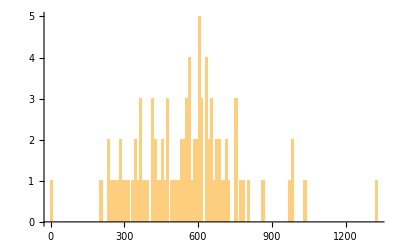

{628.229,589.306,515.687,561.582,543.062,562.146,592.126,589.606,605.403,537.561,532.748,540.419,511.378,443.51,618.677,526.824,568.221,723.36,5.22326,561.582,536.027,517.713,603.908,545.455,566.522,533.807,598.74,564.652,568.27,553.361,581.688,585.061,561.582,501.578,462.709,485.158,473.232,494.693,510.676,481.201,446.249,531.373,605.064,679.638,592.346,608.204,654.312,646.591,626.631,553.88,561.582,678.013,479.712,587.536,500.153,561.582,490.016,594.804,665.062,522.176,600.525,449.314,607.315,496.807,536.082,561.582,628.908,679.343,492.767,591.614,561.582,614.424,560.42,597.598,545.741,710.945,484.879,674.959,542.377,554.822,656.636,585.014,700.361,525.127,551.197,633.706,556.678,566.487,647.288,548.657,467.656,495.759,563.126,566.177,560.039}

{446.249,700.361}

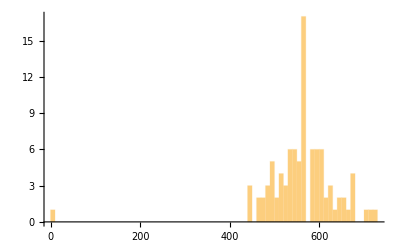

```mathematica
allWTKiValues=Normal[groupedbyMutant["WT"][All,paramKey]]

allWTVmaxValues=Normal[groupedbyMutant["WT"][All,VmaxKey]]/Normal[groupedbyMutant["WT"][All,scaleFactorKey]]/((Normal[groupedbyMutant["WT"][All,VmaxKey]]/Normal[groupedbyMutant["WT"][All,scaleFactorKey]]));

wtMedian=Median[allWTKiValues]

wtVmaxMedian=Median[allWTVmaxValues]

(* calculate 95% confidence bounds on both WT parameters *)

wtKiCIs=Quantile[allWTKiValues,{0.025,0.975}]
wtVmaxCIs=Quantile[allWTVmaxValues,{0.025,0.975}]

(* plot distribution of WT Ki values *)
Histogram[allWTKiValues,{10.},PlotRange->All]

normalizedWTvalues=Table[Normal[groupedbyMutant["WT"][n,paramKey]]/normalizationData[Normal[groupedbyMutant["WT",n,"UniqueExptID"]]],{n,1,Length[allWTKiValues]}]

wtNormalizedKiCIs=Quantile[normalizedWTvalues,{0.025,0.975}]

Histogram[normalizedWTvalues,{10.},PlotRange->All]
```

#### Some code to facilitate automatic plotting and legending (evaluate cell below):

Just lists of colors, plotmarkers, and dashing types, so that each experiment gets its own plot marker, color, and dashing type:

```mathematica
xticks={{{0.1,0},{0.5,0.5},{1,1},{5,5},{10,10},{50,50},{500,500},{5000,5000}},None};
xticks2={{{0.01,0},{0.1,0.1},{0.5,0.5},{1,1},{5,5},{10,10},{50,50},{500,500},{5000,5000}},None};

colorMap=Association[Table[datasetsIn[[n]]->ColorData[24,n-1],{n,1,Length[datasetsIn]}]]

plotMarkerList={●,○,◆,◇,■,□,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●};

dashingList={Dashing[None],Dashing[0.05],Dashing[0.015],Dashing[0.03],Dotted,Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None]};

dashingListLeg={Dashing[None],Dashing[0.05*5],Dashing[0.015*5],Dashing[0.03*5],Dotted,Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None]};
```

<|/180614_S3_d1_cMUP_1_GlyScan.csv→RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],/180710_S3d1_cMUP_1_GlyScan_GlyScan.csv→RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],/180614_S2_d1_cMUP_1_GlyScan.csv→RGBColor[1., 0.7215686274509804, 0.2196078431372549],/180402_S4_d3_cMUP_1_ValScan.csv→RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],/180528_S3_d2_cMUP_1_ValScan.csv→RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],/190318_S3_d1_cMUP_1_ValScan.csv→RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],/190407_S3_d1_cMUP_1_GlyScan.csv→RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],/180528_S3_d1_cMUP_1_ValScan.csv→RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],/190626_S2_d1_cMUP_1_SlowChip.csv→RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],/190609_S2_d1_cMUP_1_SlowChip.csv→RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],/190707_S2_d1_cMUP_2_SlowChip.csv→RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],/191128_S2_d3_cMUP_1_SlowestChip.csv→RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786]|>

```mathematica
expIndexAssociation=<|"/180614_S3_d1_cMUP_1_GlyScan.csv"->1,"/180710_S3d1_cMUP_1_GlyScan_GlyScan.csv"->2,"/180614_S2_d1_cMUP_1_GlyScan.csv"->3,"/180528_S3_d2_cMUP_1_ValScan.csv"->4,"/190318_S3_d1_cMUP_1_ValScan.csv"->5,"/190407_S3_d1_cMUP_1_GlyScan.csv"->6,"/180402_S4_d3_cMUP_1_ValScan.csv"->7,"/180528_S3_d1_cMUP_1_ValScan.csv"->8,"/190626_S2_d1_cMUP_1_SlowChip.csv"->9,"/190609_S2_d1_cMUP_1_SlowChip.csv"->10,"/190707_S2_d1_cMUP_2_SlowChip.csv"->11,"/191128_S2_d3_cMUP_1_SlowestChip.csv"->12|>
```

<|/180614_S3_d1_cMUP_1_GlyScan.csv→1,/180710_S3d1_cMUP_1_GlyScan_GlyScan.csv→2,/180614_S2_d1_cMUP_1_GlyScan.csv→3,/180528_S3_d2_cMUP_1_ValScan.csv→4,/190318_S3_d1_cMUP_1_ValScan.csv→5,/190407_S3_d1_cMUP_1_GlyScan.csv→6,/180402_S4_d3_cMUP_1_ValScan.csv→7,/180528_S3_d1_cMUP_1_ValScan.csv→8,/190626_S2_d1_cMUP_1_SlowChip.csv→9,/190609_S2_d1_cMUP_1_SlowChip.csv→10,/190707_S2_d1_cMUP_2_SlowChip.csv→11,/191128_S2_d3_cMUP_1_SlowestChip.csv→12|>

#### Bootstrap functions (for p-value calculation and parameter error estimates) (evaluate hidden cell below):

'bsMedian' returns p-values for the following parameters, in the same order: {kcat, KM, kcat/KM}

```mathematica
Needs["HypothesisTesting`"]

bsMedianIteration[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS},

wtRS=median2[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[wtIn]]];
mutRS=median2[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[mutantKIswithCIs]]];

tstar=Abs[mutRS-wtRS]

]

bsMedian[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS,checkpoint1,checkpoint2,checkpoint3},

weightedMean=median2[mutantKIswithCIs];

If[Head[weightedMean]==Median,Return[{Indeterminate,Indeterminate,Indeterminate,Indeterminate}];Continue[]];

weightedWTMean=median2[wtIn];

tobs=Abs[(weightedMean-weightedWTMean)];

tstar=Table[bsMedianIteration[mutantKIswithCIs,wtIn],{100}];

(* calculate for kcat, Km, and kcat/Km simultaneously for speed *)
checkpoint1=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/100*1.0,{n,1,4}];

If[checkpoint1[[1]]>0.1&&checkpoint1[[2]]>0.1&&checkpoint1[[3]]>0.1&&checkpoint1[[4]]>0.1,

Return[checkpoint1],

tstar=Table[bsMedianIteration[mutantKIswithCIs,wtIn],{1000}];

checkpoint2=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/1000*1.0,{n,1,4}];

If[checkpoint2[[1]]>0.01&&checkpoint2[[2]]>0.01&&checkpoint2[[3]]>0.01&&checkpoint2[[4]]>0.01,

Return[checkpoint2],

tstar=Table[bsMedianIteration[mutantKIswithCIs,wtIn],{numStatsBootstraps}];

checkpoint3=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/numStatsBootstraps*1.0,{n,1,4}];

Return[checkpoint3]]

];

]

bsMeanIteration[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS},

wtRS=Mean[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[wtIn]]];
mutRS=Mean[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[mutantKIswithCIs]]];

tstar=Abs[mutRS-wtRS]

]

bsMean[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS,checkpoint1,checkpoint2,checkpoint3},

weightedMean=Mean[mutantKIswithCIs];

weightedWTMean=Mean[wtIn];

tobs=Abs[(weightedMean-weightedWTMean)];

tstar=Table[bsMeanIteration[mutantKIswithCIs,wtIn],{100}];

(* calculate for kcat, Km, and kcat/Km simultaneously for speed *)
checkpoint1=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/100*1.0,{n,1,4}];

If[checkpoint1[[1]]>0.1&&checkpoint1[[2]]>0.1&&checkpoint1[[3]]>0.1&&checkpoint1[[4]]>0.1,

Return[checkpoint1],

tstar=Table[bsMeanIteration[mutantKIswithCIs,wtIn],{1000}];

checkpoint2=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/1000*1.0,{n,1,4}];

If[checkpoint2[[1]]>0.01&&checkpoint2[[2]]>0.01&&checkpoint2[[3]]>0.01&&checkpoint2[[4]]>0.01,

Return[checkpoint2],

tstar=Table[bsMeanIteration[mutantKIswithCIs,wtIn],{numStatsBootstraps}];

checkpoint3=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/numStatsBootstraps*1.0,{n,1,4}];

Return[checkpoint3]]

];

]

(* function for bootstrapping residuals - to get parameter estimate errors *)

bsResidual[fitModel_,numBootstraps_]:=Module[{model,data,residuals,bootstraps,concentrations,reshuffled,newData,newFit,newParams},

(* extract input experimental data from FittedModel *)
model=fitModel;
data=model["Data"];

(* extract residuals *)
residuals=model["FitResiduals"];

(* reshuffle residuals and bootstrap (looped) *)
bootstraps=Table[
concentrations=data[[All,1]];

reshuffled=RandomChoice[residuals,Length[residuals]];

newData=Table[{concentrations[[n]],model[concentrations[[n]]]+reshuffled[[n]]},{n,1,Length[concentrations]}];

newFit=NonlinearModelFit[newData,{Vmax*substrate/(KM+substrate),KM>0&&Vmax>0},{Vmax,KM},substrate];

newParams=newFit["BestFitParameters"];

{Vmax/.newParams,KM/.newParams},{numBootstraps}]

]

bsStdDevIteration[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS},

wtRS=StandardDeviation[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[wtIn]]];
mutRS=StandardDeviation[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[mutantKIswithCIs]]];

tstar=Abs[mutRS-wtRS]

]

bsStdDev[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS,checkpoint1,checkpoint2,checkpoint3},

weightedMean=StandardDeviation[mutantKIswithCIs];

If[Head[weightedMean]==StandardDeviation,Return[{Indeterminate,Indeterminate,Indeterminate}];Continue[]];

weightedWTMean=StandardDeviation[wtIn];

tobs=Abs[(weightedMean-weightedWTMean)];

tstar=Table[bsStdDevIteration[mutantKIswithCIs,wtIn],{100}];

(* calculate for kcat, Km, and kcat/Km simultaneously for speed *)
checkpoint1=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/100*1.0,{n,1,3}];

If[checkpoint1[[1]]>0.1&&checkpoint1[[2]]>0.1&&checkpoint1[[3]]>0.1,

Return[checkpoint1],

tstar=Table[bsStdDevIteration[mutantKIswithCIs,wtIn],{1000}];

checkpoint2=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/1000*1.0,{n,1,3}];

If[checkpoint2[[1]]>0.01&&checkpoint2[[2]]>0.01&&checkpoint2[[3]]>0.01,

Return[checkpoint2],

tstar=Table[bsStdDevIteration[mutantKIswithCIs,wtIn],{numStatsBootstraps}];

checkpoint3=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/numStatsBootstraps*1.0,{n,1,3}];

Return[checkpoint3]]

];

]

colorPVal[pvalue_,cutoff_]:=If[pvalue≠"N/A",Which[pvalue<cutoff&&pvalue≠0.,Style[ToString[pvalue],Bold,ColorData[20,8]],pvalue==0.,Style["<"<>ToString[1.0/numStatsBootstraps],Bold,ColorData[20,8]],pvalue≥cutoff,ToString[pvalue]],"N/A"]
```

#### Structure mapping function:

```mathematica
pafa=Import["/Users/craig/Documents/Biochemistry/Reference/Structures/5tj3.pdb",ColorFunction->Function[{x},Directive[GrayLevel[0.8],Opacity[0.7]]]];

seq=Import["/Users/craig/Documents/Biochemistry/Reference/Structures/5tj3.pdb","Sequence"];

seqJoined=Join@@{Table[{n+23,StringTake[seq[[1]],{n}]},{n,1,StringLength[seq[[1]]]}],Table[{n+374,StringTake[seq[[2]],{n}]},{n,1,StringLength[seq[[2]]]}]};

coords=Import["/Users/craig/Documents/Biochemistry/Reference/Structures/5tj3.pdb","ResidueCoordinates"];

pafaAS=Import["/Users/craig/Dropbox/HTMEK_processing/desktop_move_200110/pafa_active_site_wLigands.pdb",ColorFunction->Function[{x},GrayLevel[0.8]]];

joined=Join[coords[[1]],coords[[2]]];

coordsJoined=joined;

cAlphaAssociation=Join[AssociationThread[seqJoined[[All,1]],coordsJoined[[All,2]]],Association[{21->{2535.,-1901.6,5793.},22->{2535.,-1901.6,5793.},23->{2535.,-1901.6,5793.},373->{-1794.2,-2367.6,1819.9},374->{-1553.7,-2917.8999999999996,1116.},546->{568.5,-1399.9,5539.099999999999}}]];

makeStructureNice[res_,mutation_]:=Module[{test2},test2=ListPointPlot3D[Callout[{cAlphaAssociation[res]},Style[mutation,18,Black],{1895.1,-25.,3038.1}],PlotStyle->Directive[PointSize[0.05],Darker[Red]]];

If[mutation≠"WT",Show[pafa,pafaAS,test2,Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,1,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,2,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,3,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,4,1]],150]}],ViewPoint -> {0.06632417997547935, -6.105008189695307, -3.7111895933377492}/7, 
  ViewVertical -> {-0.6985872717587375, 0.712147563133245, 0.06943826077937733},ImageSize->500],Show[pafa,pafaAS,Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,1,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,2,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,3,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,4,1]],150]}],ViewPoint -> {0.06632417997547935, -6.105008189695307, -3.7111895933377492}/7, 
  ViewVertical -> {-0.6985872717587375, 0.712147563133245, 0.06943826077937733},ImageSize->500]]]

makeStructureNiceDM[res1_,res2_,mutation_]:=Module[{test2,test3},test2=ListPointPlot3D[Callout[{cAlphaAssociation[res1]},Style[mutation,18,Black],{1895.1,-25.,3038.1}],PlotStyle->Directive[PointSize[0.05],Darker[Red]]];

test3=ListPointPlot3D[{cAlphaAssociation[res2]},PlotStyle->Directive[PointSize[0.05],Darker[Red]]];

Show[pafa,pafaAS,test2,test3,Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,1,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,2,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,3,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,4,1]],150]}],ViewPoint -> {0.06632417997547935, -6.105008189695307, -3.7111895933377492}/7, 
  ViewVertical -> {-0.6985872717587375, 0.712147563133245, 0.06943826077937733},ImageSize->500]]
```

#### Function for statistical analysis, make aggregate plots, and output a dataset with aggregate plots, kinetic parameters, p-values etc. (evaluate hidden cell below):

```mathematica
(* association containing expression numbers, applied to 1000uM [cMUP] only *)
allData=Join@@datasets;
highestSonly=allData[Select[#ExpIndex==1&]];
allGroupedByMutantFast=highestSonly[Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&]][GroupBy["MutantID"]];
allGroupedByMutantSlow=highestSonly[Select[#ChipType=="SlowChip"&]][GroupBy["MutantID"]];
allGroupedByMutantSlowest=highestSonly[Select[#ChipType=="SlowestChip"&]][GroupBy["MutantID"]];

expressionDataFast=Association[Table[allGroupedByMutantFast[mut,1,"MutantID"]->{Length[allGroupedByMutantFast[mut]],Length[allGroupedByMutantFast[mut][Select[#EnzymeConc>0.3&]]],N[Length[allGroupedByMutantFast[mut][Select[#EnzymeConc>0.3&]]]/Length[allGroupedByMutantFast[mut]]],Normal[allGroupedByMutantFast[mut][All,"EnzymeConc"]]},{mut,1,Length[allGroupedByMutantFast]}]];

expressionDataSlow=Association[Table[allGroupedByMutantSlow[mut,1,"MutantID"]->{Length[allGroupedByMutantSlow[mut]],Length[allGroupedByMutantSlow[mut][Select[#EnzymeConc>0.3&]]],N[Length[allGroupedByMutantSlow[mut][Select[#EnzymeConc>0.3&]]]/Length[allGroupedByMutantSlow[mut]]],Normal[allGroupedByMutantSlow[mut][All,"EnzymeConc"]]},{mut,1,Length[allGroupedByMutantSlow]}]];

expressionDataSlowest=Association[Table[allGroupedByMutantSlowest[mut,1,"MutantID"]->{Length[allGroupedByMutantSlowest[mut]],Length[allGroupedByMutantSlowest[mut][Select[#EnzymeConc>0.3&]]],N[Length[allGroupedByMutantSlowest[mut][Select[#EnzymeConc>0.3&]]]/Length[allGroupedByMutantSlowest[mut]]],Normal[allGroupedByMutantSlowest[mut][All,"EnzymeConc"]]},{mut,1,Length[allGroupedByMutantSlowest]}]];

(* WT fast and slow chip data separated *)

sortedWTbyChipType=groupedbyMutant["WT"][All,{"UniqueExptID","ChipType",paramKey}][GroupBy["ChipType"]];

fastChipDataWT={#[[2]],#[[2]]/normalizationData[#[[1]]]}&/@Values[Join[Normal[sortedWTbyChipType["GlyScan",All,{"UniqueExptID",paramKey}]],Normal[sortedWTbyChipType["ValScan",All,{"UniqueExptID",paramKey}]]]];

slowChipDataWT={#[[2]],#[[2]]/normalizationData[#[[1]]]}&/@Values[Normal[sortedWTbyChipType["SlowChip",All,{"UniqueExptID",paramKey}]]];



makeAggDataset[mutant_]:=Module[{mutantID,enzymeConcs,expts,chipTypes},

mutantID=Normal[groupedbyMutant[mutant,1,"MutantID"]];

expts=Table[Normal[groupedbyMutant[mutant,n,"UniqueExptID"]],{n,1,Length[groupedbyMutant[mutant]]}];

exptsTrimmedNames=Table[StringTake[Normal[groupedbyMutant[mutant,n,"UniqueExptID"]],11],{n,1,Length[groupedbyMutant[mutant]]}];

chipTypes=Table[Normal[groupedbyMutant[mutant,n,"ChipType"]],{n,1,Length[groupedbyMutant[mutant]]}];

lbrs=Table[Normal[groupedbyMutant[mutant,n,"LocalBackgroundRatio"]],{n,1,Length[groupedbyMutant[mutant]]}];

r2s=Table[Normal[groupedbyMutant[mutant,n,"FitR2"]],{n,1,Length[groupedbyMutant[mutant]]}];

chambers=Table[ToExpression[Normal[groupedbyMutant[mutant,n,"Indices"]]],{n,1,Length[groupedbyMutant[mutant]]}];

enzymeConcs=Table[Normal[groupedbyMutant[mutant,n,"EnzymeConc"]],{n,1,Length[groupedbyMutant[mutant]]}];

substrateConcs=Table[Normal[groupedbyMutant[mutant,n,"SubstrateConc"]],{n,1,Length[groupedbyMutant[mutant]]}];

mutantKIsRaw=Normal[groupedbyMutant[mutant,All,"KiInhibitionFit"]];

VmaxScaledFit=Table[Normal[groupedbyMutant[mutant,n,VmaxKey]],{n,1,Length[groupedbyMutant[mutant]]}];

fitData=ToExpression[Normal[groupedbyMutant[mutant,All,dataKey]]];
data=Table[{#[[1]],#[[2]]}&/@fitData[[n]],{n,1,Length[groupedbyMutant[mutant]]}];

(* get min (non-zero) and max [I] *)
highLowIlimits={Min[Select[#[[All,1]],#≠0&]],Max[#[[All,1]]]}&/@ToExpression[Normal[groupedbyMutant[mutant,All,"KiFitDataPoints"]]];

(* check mutant Ki data for tight and weak Ki limits (Ki<KiFlag), and if so, replace with Ki=lowest [I]/2 and a limit flag *)
(* MAY WANT THIS AS A TABLE - CHECK *)
mutantKIData=Table[Which[mutantKIsRaw[[n]]<(highLowIlimits[[n,1]]/2),{highLowIlimits[[n,1]]/2,-1},mutantKIsRaw[[n]]>highLowIlimits[[n,2]]*2,{mutantKIsRaw[[n]],1},(highLowIlimits[[n,1]]/2)≤mutantKIsRaw[[n]]≤ highLowIlimits[[n,2]]*2,{mutantKIsRaw[[n]],0}],{n,1,Length[groupedbyMutant[mutant]]}];

mutantKILimitTable=mutantKIData[[All,2]];

cmupKM=If[MissingQ[cmupKMs[mutant,1,"KMMedian"]],cmupKMs["WT",1,"KMMedian"],cmupKMs[mutant,1,"KMMedian"]];

(* now correct these KI values by their measured cMUP KM values - have to do this again in case some have changed based on calculation above *)
correctedKIValues=Table[KiCorrection[mutantKIData[[n,1]], cmupKM,substrateConcs[[n]]],{n,1,Length[mutantKIData]}];

(* determine if enough Kis are limits to define the aggregate estimate as a limit *)
aggKILimit1=If[Length[Select[mutantKILimitTable,#==0&]]/Length[mutantKILimitTable]>0.5,0,Select[mutantKILimitTable,#≠0&][[1]]];

(* going to need to add correction limits *)
limitFromKMCorrection=cmupKMs[mutant,1,"KMAggLimit"];

aggKILimit=If[limitFromKMCorrection==-1,-1,aggKILimit1];

chengPrussoffCorrectionFactors=(mutantKIsRaw/correctedKIValues);


(* normalize corrected Ki values - has to be done after correction because measured at different [cMUP] *)

KIsNormalized=Table[correctedKIValues[[n]]/normalizationData[Normal[groupedbyMutant[mutant,n,"UniqueExptID"]]],{n,1,Length[groupedbyMutant[mutant]]}];

numberMutants=Length[Normal[groupedbyMutant[mutant,All,paramKey]]];


(* bootstrap hypothesis testing - median *)
(*pvaluesMedianRaw=bsMedianLinear[mutantData,allWTKiValues];*)
pvaluesMedianRaw=bsMedian[{#,#,#,#}&/@correctedKIValues,{#,#,#,#}&/@allWTKiValues][[1]];
pvaluesMedian=bsMedian[{#,#,#,#}&/@KIsNormalized,{#,#,#,#}&/@normalizedWTvalues][[1]];

(* bootstrap hypothesis testing - mean *)
(* currently testing on KIsNormalized *)
pvaluesMean=bsMean[{#,#,#,#}&/@KIsNormalized,{#,#,#,#}&/@normalizedWTvalues][[1]];


tooSlowFastChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&]]];
tooSlowSlowChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType=="SlowChip"&]]];
tooSlowSlowestChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType=="SlowestChip"&]]];

lbrsFast=Select[Table[Values[Normal[groupedbyMutant[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[groupedbyMutant[mutant]]}],#[[2]]≠"SlowChip"&&#[[2]]≠"SlowestChip"&][[All,1]];
lbrsSlow=Select[Table[Values[Normal[groupedbyMutant[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[groupedbyMutant[mutant]]}],#[[2]]=="SlowChip"&][[All,1]];
lbrsSlowest=Select[Table[Values[Normal[groupedbyMutant[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[groupedbyMutant[mutant]]}],#[[2]]=="SlowestChip"&][[All,1]];

fractionCulledFast=Round[N[1-(Length[lbrsFast])/(Length[lbrsFast]+Length[tooSlowFastChip])],0.01];
fractionCulledSlow=Round[N[1-(Length[lbrsSlow])/(Length[lbrsSlow]+Length[tooSlowSlowChip])],0.01];
fractionCulledSlowest=Round[N[1-(Length[lbrsSlowest])/(Length[lbrsSlowest]+Length[tooSlowSlowestChip])],0.01];

lbrHistFast=Histogram[Join[lbrsFast,If[Length[tooSlowFastChip]==0,{},Normal[tooSlowFastChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},FrameLabel->{"Local Limit of Quantification","Counts"},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledFast]<>" (Tier 1)",14],ImageScaled[{0.7,0.9}]]}];

lbrHistSlow=Histogram[Join[lbrsSlow,If[Length[tooSlowSlowChip]==0,{},Normal[tooSlowSlowChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"Local Limit of Quantification","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledSlow]<>" (Tier 2)",14],ImageScaled[{0.7,0.9}]]}];

lbrHistSlowest=Histogram[Join[lbrsSlowest,If[Length[tooSlowSlowestChip]==0,{},Normal[tooSlowSlowestChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"Local Limit of Quantification","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledSlowest]<>" (Tier 3)",14],ImageScaled[{0.7,0.9}]]}];

lbrHist=Grid[{{lbrHistFast},{If[Length[Join[lbrsSlow,If[Length[tooSlowSlowChip]==0,{},Normal[tooSlowSlowChip[All,"LocalBackgroundRatio"]]]]]==0,{},lbrHistSlow]},{If[Length[Join[lbrsSlowest,If[Length[tooSlowSlowestChip]==0,{},Normal[tooSlowSlowestChip[All,"LocalBackgroundRatio"]]]]]==0,{},lbrHistSlowest]}}];

expressionHist=Grid[{{If[MissingQ[expressionDataFast[mutant]],{},Histogram[expressionDataFast[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[E] (nM)","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataFast[mutant][[3]]]<>" (Tier 1)",14],ImageScaled[{0.7,0.9}]]]]},If[MissingQ[expressionDataSlow[mutant]],{},{Histogram[expressionDataSlow[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[E] (nM)","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataSlow[mutant][[3]]]<>" (Tier 2)",14],ImageScaled[{0.7,0.9}]]]}],If[MissingQ[expressionDataSlowest[mutant]],{},{Histogram[expressionDataSlowest[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[E] (nM)","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataSlowest[mutant][[3]]]<>" (Tier 3)",14],ImageScaled[{0.7,0.9}]]]}]}];


(* replicate plot as a function of experiment - Ki *)
getExptMeanIn=Gather[Table[{expts[[expt]],KIsNormalized[[expt]],mutant},{expt,1,Length[expts]}],#1[[1]]==#2[[1]]&];
getExptMeanInUnnormed=Gather[Table[{expts[[expt]],correctedKIValues[[expt]],mutant},{expt,1,Length[expts]}],#1[[1]]==#2[[1]]&];
(* calculate per-experiment mean *)
getExptMean={#[[1,1]],Mean[#[[All,2]]],#[[1,3]]}&/@getExptMeanIn;
getExptMeanUnnormed={#[[1,1]],Mean[#[[All,2]]],#[[1,3]]}&/@getExptMeanInUnnormed;

forRepPlotNorm=Flatten[Table[Table[{Style[{expIndexAssociation[getExptMeanIn[[mut,n,1]]],getExptMeanIn[[mut,n,2]]},Darker[colorMap[getExptMeanIn[[mut,n,1]]]]],getExptMeanIn[[mut,n,2]],getExptMeanIn[[mut,n,3]],Darker[colorMap[getExptMeanIn[[mut,n,1]]]],getExptMeanIn[[mut,n,1]]},{n,1,Length[getExptMeanIn[[mut]]]}],{mut,1,Length[getExptMeanIn]}],1];

forRepPlotNormMean=Table[{Style[Callout[{expIndexAssociation[getExptMean[[expt,1]]],getExptMean[[expt,2]]},getExptMean[[expt,3]]],colorMap[getExptMean[[expt,1]]]],getExptMean[[expt,2]],getExptMean[[expt,3]],colorMap[getExptMean[[expt,1]]],getExptMean[[expt,1]]},{expt,1,Length[getExptMean]}];

forRepPlotUnnorm=Flatten[Table[Table[{Style[{expIndexAssociation[getExptMeanInUnnormed[[mut,n,1]]],getExptMeanInUnnormed[[mut,n,2]]},Directive[GrayLevel[0.75],Opacity[0.25]]],getExptMeanInUnnormed[[mut,n,2]],getExptMeanInUnnormed[[mut,n,3]],Directive[GrayLevel[0.75],Opacity[0.25]],getExptMeanInUnnormed[[mut,n,1]]},{n,1,Length[getExptMeanInUnnormed[[mut]]]}],{mut,1,Length[getExptMeanInUnnormed]}],1];

forRepPlotUnnormMean=Table[{Style[{expIndexAssociation[getExptMeanUnnormed[[expt,1]]],getExptMeanUnnormed[[expt,2]]},Directive[GrayLevel[0.75],Opacity[0.25]]],getExptMeanUnnormed[[expt,2]],getExptMeanUnnormed[[expt,3]],Directive[GrayLevel[0.75],Opacity[0.25]],getExptMeanUnnormed[[expt,1]]},{expt,1,Length[getExptMeanUnnormed]}];

replicatesVexpt=Show[ListLogPlot[forRepPlotUnnormMean[[All,1]],PlotStyle->Directive[GrayLevel[0.5],Opacity[0.2],PointSize[0.025]],AspectRatio->0.8,Frame->True,FrameLabel->{"Experiment","K_i (μM)"},FrameStyle->Directive[20,Black],Axes->False,PlotRange->{{0,12.5},{1.0,30000.0}},ImageSize->440,PlotTheme->"Detailed",Prolog->{{Opacity[0.1,Gray],Rectangle[{8,-1 10^4},{12.5,1*^4}]}},Epilog->Inset[SwatchLegend[{Directive[GrayLevel[0.5],Opacity[0.2]]},{Style["Unnorm.",16]}],Scaled[{0.8,0.85}]]],ListLogPlot[forRepPlotUnnorm[[All,1]],PlotStyle->Directive[GrayLevel[0.5],Opacity[0.2],PointSize[0.01]],AspectRatio->0.8,Frame->True,Axes->False,ImageSize->600,PlotTheme->"Detailed"],ListLogPlot[forRepPlotNormMean[[All,1]],PlotStyle->PointSize[0.025],AspectRatio->0.8,Frame->True,FrameLabel->{"Experiment","K_i (μM)"},FrameStyle->Directive[20,Black],Axes->False,PlotRange->{{0,19},{0.01,2000.0}},ImageSize->440,PlotTheme->"Detailed",Prolog->{Opacity[0.1,Gray],Rectangle[{14,-1 10^4},{20,1*^4}]}],ListLogPlot[forRepPlotNorm[[All,1]],PlotStyle->PointSize[0.01],AspectRatio->0.8,Frame->True,Axes->False,ImageSize->600,PlotTheme->"Detailed"]];


merged=Table[{chipTypes[[n]],correctedKIValues[[n]],KIsNormalized[[n]]},{n,1,Length[chipTypes]}];

(* modified for KnownMutants *)
fastChipData=Select[merged,#[[1]]=="ValScan"||#[[1]]=="GlyScan"&];
slowChipData=Select[merged,#[[1]]=="SlowChip"&];

slowestChipData=Select[merged,#[[1]]=="SlowestChip"&];

KiHistNorm=Histogram[Log[2,{fastChipDataWT[[All,2]],fastChipData[[All,3]],slowChipData[[All,3]],slowestChipData[[All,3]]}],20,PlotRange->All,ImageSize->440,ChartStyle->{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"log_2(K_(i,Normalized)) (μM)","Counts"},Epilog->{Inset[Style["K_i Norm.",18,FontFamily->"Arial",SingleLetterItalics->False,If[pvaluesMedian<0.01,ColorData[20,8],Black]],ImageScaled[{0.25,0.8}]],Inset[SwatchLegend[{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},{Style["WT FastChip",14,FontFamily->"Arial"],Style["Mut. FastChip",14,FontFamily->"Arial"],Style["Mut. SlowChip",14,FontFamily->"Arial"]}],ImageScaled[{0.8,0.8}]]}];

exptsPlotted={};
exptsPlottedLegend={};
exptsPlottedXNorm={};

fitPlotNorm=Show[Table[

AppendTo[exptsPlottedXNorm,expts[[n]]];exptCount=Count[exptsPlottedXNorm,expts[[n]]];

Show[

ListLogLinearPlot[ReplacePart[({#[[1]]/normalizationData[Normal[groupedbyMutant[mutant,n,"UniqueExptID"]]]/(chengPrussoffCorrectionFactors[[n]]),#[[2]]}&/@data[[n]]),{1,1}->0.01],PlotStyle->Directive[colorMap[expts[[n]]]],PlotRange->{{All,Max[data[[n]][[All,1]]]*5.0},{0,Max[data[[n]][[All,2]]]*1.1}},Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks2},GridLinesStyle->Black,ImageSize->450,GridLinesStyle->Gray,PlotLabel->Style["Normalized to per-expt WT K_i",Black,18,FontFamily->"Arial"],FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)","Norm. Rate"},PlotRange->{{All,Max[data[[n]][[All,1]]]*1.2},All},PlotMarkers->{plotMarkerList[[exptCount]],Medium}],

LogLinearPlot[(VmaxScaledFit[[n]]/(1+(x)/KIsNormalized[[n]])),{x,0.01,10000},PlotStyle->Directive[colorMap[expts[[n]]],dashingList[[exptCount]]],PlotRange->{{All,Max[data[[n]][[All,1]]]*5.0},{0,Max[data[[n]][[All,2]]]*1.1}},Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks2},GridLinesStyle->Black,ImageSize->450,GridLinesStyle->Gray,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)","Norm. Rate"}]

],{n,1,Length[data]}],

LogLinearPlot[{wtVmaxCIs[[1]]/(1+x/wtNormalizedKiCIs[[1]]),wtVmaxCIs[[2]]/(1+x/wtNormalizedKiCIs[[2]])},{x,0.01,10000},PlotStyle->None,FillingStyle->Directive[Gray,Opacity[0.1]],Filling->(1->{2})],Epilog->{Inset[Style[Normal[groupedbyMutant[mutant,1,"MutantID"]],18,FontFamily->"Arial"],ImageScaled[{0.25,0.36}]],Inset[Style["n="<>ToString[Length[VmaxScaledFit]],18,FontFamily->"Arial"],ImageScaled[{0.25,0.275}]]}];

repData=Join[{{Style["Experiment",Bold],Style["Chip Type",Bold],Style["Plot Legend",Bold],Style["Column",Bold],Style["Row",Bold],Style["K_i (μM)",Bold],Style["K_i Norm. (μM)",Bold],Style["p-value",Bold],Style["LBR",Bold]}},Table[

AppendTo[exptsPlottedLegend,expts[[n]]];exptCountLeg=Count[exptsPlottedLegend,expts[[n]]];

{expts[[n]],chipTypes[[n]],Row[{Style[plotMarkerList[[exptCountLeg]],colorMap[expts[[n]]]]," ",Graphics[{dashingListLeg[[exptCountLeg]],colorMap[expts[[n]]],Line[{{0,0},{0.2,0}}]},AspectRatio->0.3,ImageSize->50]}],chambers[[n,1]],chambers[[n,2]],Round[correctedKIValues[[n]],0.1],Round[KIsNormalized[[n]],0.1],"",lbrs[[n]]},{n,1,Length[groupedbyMutant[mutant]]}],

{{Style["Median K_I",Bold],"","","","",Round[Median[correctedKIValues],0.1],Round[Median[KIsNormalized],0.1],colorPVal[pvaluesMedian,0.01],""},{Style["Median K_I Norm.",Bold],"","","","",Round[Median[correctedKIValues],0.1],Round[Mean[KIsNormalized],0.1],colorPVal[pvaluesMean,0.01],""}}

];

paramGrid=Grid[{{"",Style["Median",Bold],Style["StdDev",Bold],Style["p-value",Bold],Style["n_reps",Bold]},{Style["K_i (μM)",Bold],If[pvaluesMedianRaw<0.01,Style[Round[Median[Replace[correctedKIValues,Indeterminate->Nothing,1]],0.1],ColorData[20,8]],Round[Median[Replace[correctedKIValues,Indeterminate->Nothing,1]],0.1]],Round[StandardDeviation[Replace[correctedKIValues,Indeterminate->Nothing,1]],0.1],colorPVal[pvaluesMedianRaw,0.01],Length[Replace[correctedKIValues,Indeterminate->Nothing,1]]},{Style["K_i Norm. (μM)",Bold],If[pvaluesMedian<0.01,Style[Round[Median[Replace[KIsNormalized,Indeterminate->Nothing,1]],0.1],ColorData[20,8]],Round[Median[Replace[KIsNormalized,Indeterminate->Nothing,1]],0.1]],Round[StandardDeviation[Replace[KIsNormalized,Indeterminate->Nothing,1]],0.1],colorPVal[pvaluesMedian,0.01],Length[Replace[KIsNormalized,Indeterminate->Nothing,1]]},{Style["Tier 1",Bold],""},{Style["Total Chambers"],"","","",expressionDataFast[mutant][[1]]},{Style["Expressed (>0.3nM)"],"","","",expressionDataFast[mutant][[2]]},
{Style["LLoD>5&&<6 2pt fits"],"","","",(Length[lbrsFast])},

{Style["Tier 2",Bold],""},{Style["Total Chambers"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",expressionDataSlow[mutant][[1]]]},{Style["Expressed (>0.3nM)"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",expressionDataSlow[mutant][[2]]]},{Style["LLoD>5&&<6 2pt fits"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",(Length[lbrsSlow])]},

{Style["Tier 3",Bold],""},{Style["Total Chambers"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",expressionDataSlowest[mutant][[1]]]},{Style["Expressed (>0.3nM)"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",expressionDataSlowest[mutant][[2]]]},{Style["LLoD>5&&<6 2pt fits"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",(Length[lbrsSlowest])]}

},Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}];

structure=If[mutant≠"N100A/R164A",makeStructureNice[ToExpression[StringDrop[StringDrop[mutant,1],-1]],mutant],makeStructureNiceDM[100,164,"N100A/R164A"]];
summaryTable={Style[#,Bold]&/@{"Mutation","Aggregate Parameters"},{structure,paramGrid}};

forCSV=Join[Table[Association[{"Version"->notebookVersion,"RunDate"->DateString["ISODate"],"MutantID"->mutantID,"Experiment"->expts[[n]],"ChipType"->chipTypes[[n]],"Indices"->chambers[[n]],"Column"->chambers[[n,1]],"Row"->chambers[[n,2]],"EnzymeConc"->enzymeConcs[[n]],"AllInhibitorConcs"->ToExpression[Normal[groupedbyMutant[mutant,n,"AllInhibitorConcentrations"]]],"AllInitialRates"->ToExpression[Normal[groupedbyMutant[mutant,n,"AllInitialRates"]]],"SubstrateConc"->substrateConcs[[n]],"FitRSquared"->r2s[[n]],"BootstrapsFit"->"","InterceptCI"->"","kcatoverKMCI"->"",

"Ki"->correctedKIValues[[n]],"KiMean"->Mean[correctedKIValues],"KiMedian"->median2[correctedKIValues],"KiNorm"->KIsNormalized[[n]],"KiNormMean"->Mean[KIsNormalized],"KiNormMedian"->median2[KIsNormalized],

"StdDevKiNorm"->If[Length[KIsNormalized]>1,StandardDeviation[KIsNormalized],""],

"Log2StdDevKiNorm"->If[Length[KIsNormalized]>1,StandardDeviation[Log[2,KIsNormalized]],""],

"KiNormBootstrapHypothesisTestMedian"->pvaluesMedian,

"KiNormBootstrapHypothesisTestMean"->pvaluesMean,

"KiNormLimit"->mutantKILimitTable[[n]],"KiNormAggLimit"->aggKILimit,"KiNormLimitValueMedian"->median2[KIsNormalized],"KiNormLimitValueMean"->Mean[KIsNormalized],

"NumCulledReps"->Length[correctedKIValues],

"LBR"->lbrs[[n]],"RateLimit"->0,"AggRateLimit"->0

}],{n,1,Length[groupedbyMutant[mutant]]}],

Table[Association[{"Version"->notebookVersion,"RunDate"->DateString["ISODate"],"MutantID"->mutant,"Experiment"->tooSlow[mutant,n,"UniqueExptID"],"ChipType"->tooSlow[mutant,n,"ChipType"],"Indices"->ToExpression[tooSlow[mutant,n,"Indices"]],"Column"->ToExpression[tooSlow[mutant,n,"Indices"]][[1]],"Row"->ToExpression[tooSlow[mutant,n,"Indices"]][[2]],"EnzymeConc"->tooSlow[mutant,n,"EnzymeConc"],"AllInhibitorConcs"->ToExpression[Normal[tooSlow[mutant,n,"AllInhibitorConcentrations"]]],"AllInitialRates"->ToExpression[Normal[tooSlow[mutant,n,"AllInitialRates"]]],"SubstrateConc"->tooSlow[mutant,n,"SubstrateConc"],"FitRSquared"->"","BootstrapsFit"->"","InterceptCI"->"","kcatoverKMCI"->"",

"Ki"->"","KiMean"->Mean[correctedKIValues],"KiMedian"->Median[correctedKIValues],"KiNorm"->"","KiNormMean"->Mean[KIsNormalized],"KiNormMedian"->median2[KIsNormalized],

"StdDevKiNorm"->If[Length[KIsNormalized]>1,StandardDeviation[KIsNormalized],""],

"Log2StdDevKiNorm"->If[Length[KIsNormalized]>1,StandardDeviation[Log[2,KIsNormalized]],""],

"KiNormBootstrapHypothesisTestMedian"->pvaluesMedian,

"KiNormBootstrapHypothesisTestMean"->pvaluesMean,

"KiNormLimit"->"","KiNormAggLimit"->aggKILimit,"KiNormLimitValueMedian"->median2[KIsNormalized],"KiNormLimitValueMean"->Mean[KIsNormalized],

"NumCulledReps"->Length[correctedKIValues],

"LBR"->tooSlow[mutant,n,"LocalBackgroundRatio"],"RateLimit"->1,"AggRateLimit"->0

}],{n,1,If[MissingQ[tooSlow[mutant]],0,Length[tooSlow[mutant]]]}]

];

forPDF=Table[Association[{"MutantID"->mutantID,"Experiment"->expts[[n]],"Indices"->chambers[[n]],"Column"->chambers[[n,1]],"Row"->chambers[[n,2]],"Data"->"NaN","FitRSquared"->r2s[[n]],"BootstrapsFit"->"NaN","InterceptCI"->"NaN","kcatoverKMCI"->"NaN",

"Ki"->correctedKIValues[[n]],"Ki_Mean"->Mean[correctedKIValues],"Ki_Median"->Median[correctedKIValues],

"Ki_Norm"->KIsNormalized[[n]],"Ki_Norm_Mean"->Mean[KIsNormalized],"Ki_Norm_Median"->Median[KIsNormalized],

"FitPlotNorm"->fitPlotNorm,"KiHistNorm"->KiHistNorm,

"KiNormBootstrapHypothesisTestMedian"->pvaluesMedian,

"KiNormBootstrapHypothesisTestMean"->pvaluesMean,"FractionCulledHist"->lbrHist,"ExpressionHist"->expressionHist,

"KiNormBootstrapHypothesisTestMedian"->pvaluesMedian,

"KiNormBootstrapHypothesisTestMean"->pvaluesMean,

"ReplicatePlot"->replicatesVexpt,

"DataTable"->repData,"SummaryTableStructure"->Grid[Transpose[{summaryTable[[All,1]]}],Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{None,None},{LightGray,None}}],"SummaryTableParams"->Grid[Transpose[{summaryTable[[All,2]]}],Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{None,None},{LightGray,None}}]

}],{n,1,Length[groupedbyMutant[mutant]]}];

{forCSV,forPDF}

]



makeAggDatasetSlow[mutant_]:=Module[{fractionculled},

fractionCulled=1.0;

expts=Table[Normal[tooSlow[mutant,n,"UniqueExptID"]],{n,1,Length[tooSlow[mutant]]}];

tooSlowFastChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&]]];
tooSlowSlowChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType=="SlowChip"&]]];
tooSlowSlowestChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType=="SlowestChip"&]]];

lbrsFast=If[MissingQ[tooSlow[mutant]],{},Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]≠"SlowChip"&&#[[2]]≠"SlowestChip"&&#[[1]]>5.0&][[All,1]]];
lbrsSlow=If[MissingQ[tooSlow[mutant]],{},Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]=="SlowChip"&&#[[1]]>5.0&][[All,1]]];
lbrsSlowest=Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]=="SlowestChip"&&#[[1]]>5.0&][[All,1]];

fractionCulledFast=Round[N[1-(Length[lbrsFast])/(Length[lbrsFast]+Length[tooSlowFastChip])],0.01];
fractionCulledSlow=Round[N[1-(Length[lbrsSlow])/(Length[lbrsSlow]+Length[tooSlowSlowChip])],0.01];
fractionCulledSlowest=Round[N[1-(Length[lbrsSlowest])/(Length[lbrsSlowest]+Length[tooSlowSlowestChip])],0.01];

lbrHistFast=Histogram[Join[lbrsFast,If[Length[tooSlowFastChip]==0,{},Normal[tooSlowFastChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},FrameLabel->{"Local Limit of Quantification","Counts"},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledFast]<>" (Tier 1)",14],ImageScaled[{0.7,0.9}]]}];

lbrHistSlow=Histogram[Join[lbrsSlow,If[Length[tooSlowSlowChip]==0,{},Normal[tooSlowSlowChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"Local Limit of Quantification","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledSlow]<>" (Tier 2)",14],ImageScaled[{0.7,0.9}]]}];

lbrHistSlowest=Histogram[Join[lbrsSlowest,If[Length[tooSlowSlowestChip]==0,{},Normal[tooSlowSlowestChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"Local Limit of Quantification","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledSlowest]<>" (Tier 3)",14],ImageScaled[{0.7,0.9}]]}];

lbrHist=Grid[{{lbrHistFast},{If[Length[Join[lbrsSlow,If[Length[tooSlowSlowChip]==0,{},Normal[tooSlowSlowChip[All,"LocalBackgroundRatio"]]]]]==0,{},lbrHistSlow]},{If[Length[Join[lbrsSlowest,If[Length[tooSlowSlowestChip]==0,{},Normal[tooSlowSlowestChip[All,"LocalBackgroundRatio"]]]]]==0,{},lbrHistSlowest]}}];

paramGrid=Grid[{{"",Style["Median",Bold],Style["StdDev",Bold],Style["p-value",Bold],Style["n_reps",Bold]},{Style["K_i (μM)",Bold],"N/A","N/A","N/A",0},{Style["K_i Norm. (μM)",Bold],"N/A","N/A","N/A",0},{Style["Tier 1",Bold],""},{Style["Total Chambers"],"","","",If[MissingQ[expressionDataFast[mutant]],"N/A",expressionDataFast[mutant][[1]]]},{Style["Expressed (>0.3nM)"],"","","",If[MissingQ[expressionDataFast[mutant]],"N/A",expressionDataFast[mutant][[2]]]},{Style["LLoD>5&&<6 2pt fits"],"","","",(Length[lbrsFast])},

{Style["Tier 2",Bold],""},{Style["Total Chambers"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",expressionDataSlow[mutant][[1]]]},{Style["Expressed (>0.3nM)"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",expressionDataSlow[mutant][[2]]]},{Style["LLoD>5&&<6 2pt fits"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",(Length[lbrsSlow])]},

{Style["Tier 3",Bold],""},{Style["Total Chambers"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",expressionDataSlowest[mutant][[1]]]},{Style["Expressed (>0.3nM)"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",expressionDataSlowest[mutant][[2]]]},{Style["LLoD>5&&<6 2pt fits"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",(Length[lbrsSlowest])]}

},Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}];

structure=makeStructureNice[ToExpression[StringDrop[StringDrop[mutant,1],-1]],mutant];
summaryTable={Style[#,Bold]&/@{"Mutation","Aggregate Parameters"},{structure,paramGrid}};

expressionHist=Grid[{{If[MissingQ[expressionDataFast[mutant]],{},Histogram[expressionDataFast[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[E] (nM)","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataFast[mutant][[3]]]<>" (Tier 1)",14],ImageScaled[{0.7,0.9}]]]]},If[MissingQ[expressionDataSlow[mutant]],{},{Histogram[expressionDataSlow[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[E] (nM)","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataSlow[mutant][[3]]]<>" (Tier 2)",14],ImageScaled[{0.7,0.9}]]]}],If[MissingQ[expressionDataSlowest[mutant]],{},{Histogram[expressionDataSlowest[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[E] (nM)","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataSlowest[mutant][[3]]]<>" (Tier 3)",14],ImageScaled[{0.7,0.9}]]]}]}];

repData=Join[{{Style["Experiment",Bold],Style["Chip Type",Bold],Style["Plot Legend",Bold],Style["Column",Bold],Style["Row",Bold],Style["K_i (μM)",Bold],Style["K_i Norm. (μM)",Bold],Style["MeanCI (K_i)",Bold],Style["MeanCI (K_i Norm.)"],Style["p-value",Bold],Style["LLoD",Bold]}},Table[

AppendTo[exptsPlottedLegend,expts[[n]]];exptCountLeg=Count[exptsPlottedLegend,expts[[n]]];

{StringTake[tooSlow[mutant,n,"UniqueExptID"],11],tooSlow[mutant,n,"ChipType"],"",ToExpression[tooSlow[mutant,n,"Indices"]][[1]],ToExpression[tooSlow[mutant,n,"Indices"]][[2]],"","NaN","NaN","NaN","",Round[tooSlow[mutant,n,"LocalBackgroundRatio"],0.1]},{n,1,Length[groupedbyMutant[mutant]]}],

{{Style["Median K_I",Bold],"","","","","","","","","",""},{Style["Mean K_I",Bold],"","","","","","","","","",""}}

];

forCSV=Table[Association[{"Version"->notebookVersion,"RunDate"->DateString["ISODate"],"MutantID"->mutant,"Experiment"->tooSlow[mutant,n,"UniqueExptID"],"ChipType"->tooSlow[mutant,n,"ChipType"],"Indices"->ToExpression[tooSlow[mutant,n,"Indices"]],"Column"->ToExpression[tooSlow[mutant,n,"Indices"]][[1]],"Row"->ToExpression[tooSlow[mutant,n,"Indices"]][[2]],"EnzymeConc"->tooSlow[mutant,n,"EnzymeConc"],"AllInhibitorConcs"->ToExpression[Normal[tooSlow[mutant,n,"AllInhibitorConcentrations"]]],"AllInitialRates"->ToExpression[Normal[tooSlow[mutant,n,"AllInitialRates"]]],"SubstrateConc"->tooSlow[mutant,n,"SubstrateConc"],"FitRSquared"->"","BootstrapsFit"->"","InterceptCI"->"","kcatoverKMCI"->"",

"Ki"->"","KiMean"->"","KiMedian"->"","KiNorm"->"","KiNormMean"->"","KiNormMedian"->"",

"StdDevKiNorm"->"",

"Log2StdDevKiNorm"->"",

"KiNormBootstrapHypothesisTestMedian"->"",

"KiNormBootstrapHypothesisTestMean"->"",

"KiNormLimit"->"","KiNormAggLimit"->"","KiNormLimitValueMedian"->"","KiNormLimitValueMean"->"",

"NumCulledReps"->0,

"LBR"->tooSlow[mutant,n,"LocalBackgroundRatio"],"RateLimit"->1,"AggRateLimit"->1

}],{n,1,If[MissingQ[tooSlow[mutant]],0,Length[tooSlow[mutant]]]}];

forPDF=Table[Association[{"MutantID"->mutant,"Experiment"->StringTake[tooSlow[mutant,n,"UniqueExptID"],11],"Indices"->ToExpression[tooSlow[mutant,n,"Indices"]],"Column"->ToExpression[tooSlow[mutant,n,"Indices"]][[1]],"Row"->ToExpression[tooSlow[mutant,n,"Indices"]][[2]],"Data"->"NaN","FitRSquared"->"","BootstrapsFit"->"NaN","InterceptCI"->"NaN","kcatoverKMCI"->"NaN",

"Ki"->"","KiMean"->"","KiMedian"->"",

"KiNorm"->"","KiNormMean"->"","KiNormMedian"->"",

"FitPlot"->"",

"FitPlotNorm"->"","kcat/Km_NormHistogram"->"",

"KiHist"->"",

"KiHistNorm"->"",

"KiNormBootstrapHypothesisTestMedian"->"",

"KiNormBootstrapHypothesisTestMean"->"","FractionCulledHist"->lbrHist,"ExpressionHist"->expressionHist,

"KiNormBootstrapHypothesisTestMedian"->"",

"KiNormBootstrapHypothesisTestMean"->"",

"ReplicatePlot"->"",

"DataTable"->repData,"SummaryTableStructure"->Grid[Transpose[{summaryTable[[All,1]]}],Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{None,None},{LightGray,None}}],"SummaryTableParams"->Grid[Transpose[{summaryTable[[All,2]]}],Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{None,None},{LightGray,None}}]

}],{n,1,Length[groupedbyMutant[mutant]]}];

{forCSV,forPDF}

]
```

```mathematica
SeedRandom[2020]

Dynamic[mutantIterator]

culledLength=Length[mutantsWithData];
dropLength=Length[unmeasured];

(*culledLength=5;
dropLength=1;*)

start1=AbsoluteTime[];

total=Table[makeAggDataset[mutantsWithData[[mutantIterator]]],{mutantIterator,1,culledLength}];
totalSlow=Table[makeAggDatasetSlow[unmeasured[[mutantIterator]]],{mutantIterator,1,dropLength}];

outForCSV=Join[Table[Values[total[[mutantIterator,1]]],{mutantIterator,1,culledLength}],Table[Values[totalSlow[[mutantIterator,1]]],{mutantIterator,1,dropLength}]];

outForPDF=Join[Flatten[Table[total[[mutantIterator,2]],{mutantIterator,1,culledLength}],1],Flatten[Table[totalSlow[[mutantIterator,2]],{mutantIterator,1,dropLength}],1]];

AbsoluteTime[]-start1
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

StandardDeviation::shlen: The argument {529.35} should have at least two elements.

StandardDeviation::shlen: The argument {570.723} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

ListPointPlot3D::ldata: Callout[{Missing[KeyAbsent,Null]},WT,{1895.1,-25.,3038.1}] is not a valid dataset or list of datasets.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

1079.33319

```mathematica
maxExponent=Round[Log[10,$MaxMachineNumber]]+1;

testF2[in_]:=Which[NumberQ[in],ToString[NumberForm[in,ScientificNotationThreshold->{-maxExponent,maxExponent}]],ListQ[in],ToString[NumberForm[#,ScientificNotationThreshold->{-maxExponent,maxExponent}]&/@in],NumberQ[in]==False&&ListQ[in]==False,in]

keys=Keys[forCSV[[1]]]

out2=Prepend[Sort[Flatten[outForCSV,1],ToExpression[StringDrop[StringDrop[#1[[3]],-1],1]]<ToExpression[StringDrop[StringDrop[#2[[3]],-1],1]]&],keys];

(*Export["~/Desktop/test2.csv",out2]*)

Export["~/Desktop/PafA_PiInhibition_aggData_WTNorm_v2.0_201027.csv",Prepend[Map[testF2,Flatten[outForCSV,1],{2}],keys]]
```

{Version,RunDate,MutantID,Experiment,ChipType,Indices,Column,Row,EnzymeConc,AllInhibitorConcs,AllInitialRates,SubstrateConc,FitRSquared,BootstrapsFit,InterceptCI,kcatoverKMCI,Ki,KiMean,KiMedian,KiNorm,KiNormMean,KiNormMedian,StdDevKiNorm,Log2StdDevKiNorm,KiNormBootstrapHypothesisTestMedian,KiNormBootstrapHypothesisTestMean,KiNormLimit,KiNormAggLimit,KiNormLimitValueMedian,KiNormLimitValueMean,NumCulledReps,LBR,RateLimit,AggRateLimit}

~/Desktop/PafA_PiInhibition_aggData_WTNorm_v2.0_201027.csv

Number of mutants with aggregate measurement:

1002

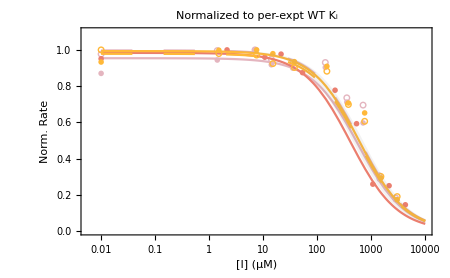
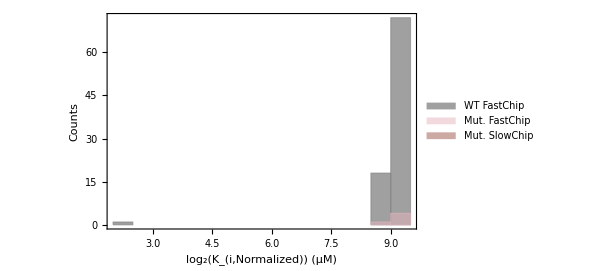
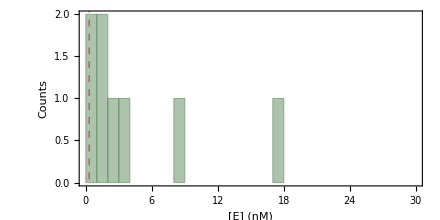
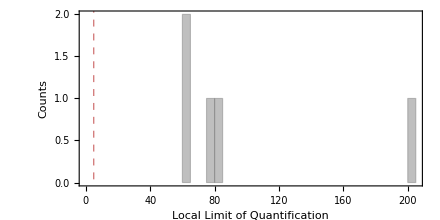
Phosphate Inhibition |  | 
Mutation
-Graphics3D- | Aggregate Parameters
 | Median | StdDev | p-value | n_reps
K_i (μM) | 396.4 | 97.2 | 0.18 | 5
K_i Norm. (μM) | 585.1 | 82.2 | 0.4 | 5
Tier 1 |  |  |  | 
Total Chambers |  |  |  | 8
Expressed (>0.3nM) |  |  |  | 7
LLoD>5&&<6 2pt fits |  |  |  | 5
Tier 2 |  |  |  | 
Total Chambers |  |  |  | N/A
Expressed (>0.3nM) |  |  |  | N/A
LLoD>5&&<6 2pt fits |  |  |  | N/A
Tier 3 |  |  |  | 
Total Chambers |  |  |  | N/A
Expressed (>0.3nM) |  |  |  | N/A
LLoD>5&&<6 2pt fits |  |  |  | N/A | Inhibition curves
-Graphics-
Inhibition fit parameters |  | 
 |  | 
-Graphics- | -Graphics- | 
Expression and Limit of Quantification |  | 
 |  | 
-Graphics-

 | -Graphics-
{}
{} | 
Experimental Data |  | 
Experiment | Chip Type | Plot Legend | Column | Row | K_i (μM) | K_i Norm. (μM) | p-value | LBR
/180614_S3_d1_cMUP_1_GlyScan.csv | GlyScan | ● -Graphics- | 28 | 42 | 406.4 | 574.3 |  | 81.84
/180614_S3_d1_cMUP_1_GlyScan.csv | GlyScan | ○ -Graphics- | 25 | 18 | 434.5 | 614. |  | 76.6488
/180710_S3d1_cMUP_1_GlyScan_GlyScan.csv | GlyScan | ● -Graphics- | 28 | 42 | 192.4 | 412.3 |  | 201.025
/180614_S2_d1_cMUP_1_GlyScan.csv | GlyScan | ● -Graphics- | 28 | 42 | 396.4 | 599.1 |  | 61.3838
/180614_S2_d1_cMUP_1_GlyScan.csv | GlyScan | ○ -Graphics- | 25 | 18 | 387.1 | 585.1 |  | 62.1115
Median K_I |  |  |  |  | 396.4 | 585.1 | 0.4 | 
Median K_I Norm. |  |  |  |  | 396.4 | 557. | 0.91 |  |  |

```mathematica
Print["Number of mutants with aggregate measurement:"]
Length[total]

datasetIn=Dataset[outForPDF];

(*Export["~/Desktop/PafA_PO4_aggData_191208.wxf",datasetIn,PerformanceGoal->"Size"]*)

(*Export["~/Desktop/PafA_PO4_aggData_191208.csv",out2,"Data"]*)

dataset=datasetIn[GroupBy["MutantID"]];

m=1;

If[m≤Length[total],
Grid[{{Style["Phosphate Inhibition",Bold,18,FontFamily->"Arial"],SpanFromLeft},{dataset[m,1,"SummaryTableStructure"],dataset[m,1,"SummaryTableParams"],Column[{Style["Inhibition curves",Bold],dataset[m,1,"FitPlotNorm"]},Frame->All,Background->{LightGray,None}]},{Style["Inhibition fit parameters",Bold],SpanFromLeft},{},{dataset[m,1,"KiHistNorm"],dataset[m,1,"ReplicatePlot"]},{Style["Expression and Limit of Quantification",Bold],SpanFromLeft},{},{dataset[m,1,"ExpressionHist"],dataset[m,1,"FractionCulledHist"]},{Style["Experimental Data",Bold],SpanFromLeft},{Grid[Normal[dataset[m,1,"DataTable"]],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}],SpanFromLeft}},Frame->True,Dividers->{{True,False,False,True,False,True,True,True},{True,True}},Background->{{None,None},{LightBlue,None,LightGray,None,None,LightGray,None,None,LightGray}},Alignment->Top,Spacings->2],

Grid[{{Column[{dataset[m,1,"SummaryTableStructure"],Grid[{{Style["Expression",Bold]},{},{dataset[m,1,"ExpressionHist"]}},Frame->True,Dividers->{{True,True,False},{True,True}},Background->{{None,None},{LightGray,None}},Alignment->Top]}],Column[{dataset[m,1,"SummaryTableParams"],Grid[{{Style["Limit of Quantification",Bold]},{},{dataset[m,1,"FractionCulledHist"]}},Frame->True,Dividers->{{True,True,False},{True,True}},Background->{{None,None},{LightGray,None}},Alignment->Top]}]},{Grid[Normal[dataset[m,1,"DataTable"]],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}],SpanFromLeft},{"",""}},Alignment->Top]
]
```

```mathematica
.
```